```mathematica
computed=Association[]
```

<||>

```mathematica
Put[computed,"d:\\embedchrom4.m"]
```

```mathematica
computed=Get["d:\\embedchrom4.m"];Length[computed]
```

1895

```mathematica
demoValues={z->3728,b06->2520,b04->3000,b07->2488,b34->1280,b02->2852,b17->1940,b05->2852,b12->2324,b26->1292,b08->2348,b22->1590,b28->1268,b35->1108,b47->264,b10->2384,b21->1596,b20->1848,b24->1500,b40->712,b03->2616,b11->2120,b15->1996,b18->1682,b43->894,b33->1112,b38->702,b01->2640,b16->1772,b14->2038,b13->2050,b41->912,b30->1112,b45->870,b27->976,b42->746,b46->224,b09->2360,b25->1558,b19->1924,b23->1598,b39->796,b32->980,b37->672,b29->1060,b44->870,b50->230,b31->980,b36->628,b49->186,b48->182}
```

{z→3728,b06→2520,b04→3000,b07→2488,b34→1280,b02→2852,b17→1940,b05→2852,b12→2324,b26→1292,b08→2348,b22→1590,b28→1268,b35→1108,b47→264,b10→2384,b21→1596,b20→1848,b24→1500,b40→712,b03→2616,b11→2120,b15→1996,b18→1682,b43→894,b33→1112,b38→702,b01→2640,b16→1772,b14→2038,b13→2050,b41→912,b30→1112,b45→870,b27→976,b42→746,b46→224,b09→2360,b25→1558,b19→1924,b23→1598,b39→796,b32→980,b37→672,b29→1060,b44→870,b50→230,b31→980,b36→628,b49→186,b48→182}

```mathematica
Min[Table[computed[key],{key,Keys[newAssoc]}]//Sort]
```

Min[0→29524,16→29608,25→51478,27→29443,27→29605,28→36194,28→36898,30→29521,30→29527,30→31984,33→29797,35→29633,38→38308,40→36817,41→7738,41→29497,41→29551,41→31714,43→29602,44→22318,46→29446,52→27337,52→31711,52→31738,53→29523,53→29525,53→49210,54→29515,54→29533,58→28795,58→30253,58→36166,62→29577,63→23072,63→27610,63→29257,63→29888,64→29560,66→11950,66→38281,68→29416,68→36736,68→39014,68→52232,68→56770,68→59048,69→448,70→22237,71→27340,71→29494,71→31444,72→22963,72→36085,72→36112,73→29440,74→29281,74→29305,74→29767,74→29768,74→30334,74→36086,76→29469,78→29574,78→46942,78→49220,79→27256,79→29176,79→29328,79→51475,80→29442,81→29434,82→9841,82→31492,82→49207,83→9844,83→29520,84→29512,85→23044,86→35434,86→36138,87→27259,87→29537,88→28792,88→29417,90→25168,90→49208,93→27364,93→31708,93→43908,94→29496,95→49972,96→11680,96→13340,96→14748,96→29706,98→4920,98→23689,98→29378,99→9763,99→28768,100→36030,101→2824,101→23041,101→28876,101→29200,101→29857,101→31954,102→20812,102→22960,102→23770,102→30586,102→35978,102→56012,103→7034,103→21967,104→7458,104→29278,104→31684,104→38254,104→51472,104→58288,105→27336,105→29542,106→7735,106→17568,106→27328,107→22038,107→29514,107→29737,108→16864,108→34620,109→9760,109→24414,109→29223,110→26608,110→33916,111→20050,111→28794,112→35353,113→22990,114→22156,114→29413,114→35406,115→29254,115→30496,116→9574,117→28873,117→29517,118→25141,118→29506,119→30262,120→11244,120→20785,120→24922,121→41650,121→49963,123→2554,123→9814,123→27334,124→7657,124→20776,124→29493,126→22817,126→22954,126→27519,126→29439,127→22964,127→29232,127→29282,127→29431,128→27282,128→29272,128→29353,129→28765,130→22234,130→36004,131→473,131→637,131→728,131→11947,131→31924,131→49200,132→9493,132→27255,132→30172,133→27247,133→29436,133→49216,134→4650,134→7654,134→27070,134→29433,134→37548,135→49204,136→16783,136→18980,136→28848,136→34539,136→45416,136→54492,137→29648,138→29296,138→33834,138→33889,139→24144,140→9112,140→15454,140→29460,140→29513,141→7707,141→28791,141→29529,142→8436,142→29173,142→33158,143→9842,143→32684,144→29350,144→36058,145→27310,145→31681,146→22720,146→22744,146→36084,146→39382,146→39392,147→7732,147→21886,147→29197,147→50718,148→23016,148→29766,150→9733,150→10998,150→26989,150→29186,150→29247,152→28767,152→28845,153→31468,154→3280,155→19969,155→20060,155→29209,156→9598,156→22951,156→27118,156→29415,156→46932,157→22227,157→22882,157→27355,158→4674,158→27330,158→29269,158→46184,159→9148,159→22315,159→25138,159→27327,159→28714,159→29488,161→46939,162→9139,162→14044,162→29174,163→29325,163→40896,164→367,164→1174,164→2733,164→23013,164→29826,165→7576,165→9838,165→9854,165→20484,165→20803,166→6779,166→27253,167→2473,168→15372,168→49196,170→1872,170→2124,170→18274,170→33050,170→52976,172→27229,172→37521,172→49206,172→50715,172→57528,173→28804,173→30010,174→19780,174→27249,175→27580,175→29405,175→29677,176→3524,176→14667,176→16160,176→22717,176→22908,176→27333,176→30082,177→22981,177→27325,177→30244,177→32441,178→9734,178→13258,178→29251,178→33157,179→10543,180→7006,181→26605,181→29736,182→7704,182→20047,182→28764,183→4222,183→9517,183→11920,183→44662,184→35326,185→22936,186→22792,186→27246,186→29407,186→35352,187→7387,187→9850,187→21510,189→29038,189→29485,189→43156,189→47694,190→13312,190→14016,190→21957,190→22856,191→27036,192→6925,192→27273,192→42404,194→31465,195→8893,195→20773,196→33808,197→400,197→5377,197→9057,197→9571,197→11944,198→27309,198→35272,199→22962,199→41640,200→168,200→22231,200→22711,200→23608,200→28687,201→22146,201→22721,201→29280,202→22789,202→29412,202→35977,202→56011,203→22312,203→22879,203→26581,203→29128,203→48451,204→16052,204→23518,204→36003,205→1171,205→1426,205→5620,205→28711,205→29502,205→31441,206→1093,206→9811,207→7483,207→20781,208→9757,208→18247,208→25114,208→29647,208→44659,209→20695,209→22662,210→22735,211→6320,211→22873,211→26527,211→49212,212→2551,212→28713,212→29487,212→33888,213→23446,214→6952,214→10552,214→22952,214→29270,215→22933,215→49198,216→27307,216→49954,217→3281,217→9599,217→23680,217→26852,217→30406,218→19699,218→19709,218→36057,219→3979,219→24898,219→27252,219→29182,220→27109,220→27244,221→7003,221→20461,221→27060,221→29170,221→29938,222→8820,222→20758,222→22287,222→29008,223→9109,224→2284,224→9490,224→29511,225→9840,225→49203,227→1146,227→7627,227→27094,228→7306,228→9503,228→20557,228→20721,228→29199,228→48460,229→22959,229→29166,229→30981,230→8811,230→22708,230→26609,231→22639,231→28786,231→29277,232→4380,232→11704,232→29404,233→286,233→377,233→29245,234→2578,235→5590,235→28065,236→29214,236→46172,237→3277,237→28777,237→40144,238→445,238→17541,238→27550,239→3199,239→3404,239→9595,239→20056,239→46936,240→7573,240→22899,241→9031,242→7455,242→29205,242→29253,242→29322,243→22207,244→8184,244→13232,244→20767,244→31224,245→12650,245→25868,246→28684,247→28552,247→29929,248→7480,248→9834,248→33862,249→9730,249→11917,249→22764,249→25111,249→27579,249→29676,251→9823,251→20775,251→30163,251→43905,251→46938,252→9491,252→9759,253→1102,253→10462,253→22953,254→27013,255→29271,256→4428,256→29191,256→48448,257→22233,257→22870,257→40887,258→7651,258→28308,258→28710,258→35325,259→22693,259→27226,260→24895,260→27228,260→28800,260→39380,261→28783,262→218,262→546,263→5374,263→27301,263→29037,264→364,264→9753,264→22613,264→33076,265→26501,266→9813,266→20040,266→22284,266→29097,267→3253,267→20794,267→29430,268→1143,268→1395,268→2203,268→49195,269→9832,269→27306,270→22855,270→30978,270→33807,270→35245,270→42392,270→55252,272→14586,272→35271,274→13176,274→16159,274→26578,274→29196,274→29406,274→31194,275→21501,276→3523,276→27490,276→31438,277→6706,277→7653,277→22636,277→22844,277→28549,280→3173,280→26732,281→9564,281→27085,281→30954,282→1800,282→9514,282→46183,283→6978,283→9111,283→26599,284→11677,284→22881,284→28785,284→42403,284→43147,284→47685,285→4132,286→391,286→13284,287→5350,288→2544,288→9526,288→22709,288→28525,288→28686,288→33130,289→7647,289→20749,289→21186,289→22153,290→26851,290→27220,291→20475,292→30001,292→39372,293→20044,293→48450,294→10300,294→46930,295→97,295→24411,296→9751,296→20692,296→29007,296→29242,297→2496,297→21876,298→11701,298→26524,298→27091,299→20533,300→26979,302→9085,302→29188,303→22225,303→22927,304→20048,304→26500,304→28624,304→29172,304→35976,304→56010,305→29250,305→49197,306→9121,306→33781,306→48456,306→53734,307→442,307→697,308→9830,308→9837,308→11217,308→20457,309→3493,309→7411,309→20754,309→24871,309→27984,310→19959,312→22935,312→27549,312→29162,313→6077,313→9568,313→22204,314→15427,315→20764,315→23365,315→40140,316→6922,316→10228,316→22852,316→27300,317→6870,317→26597,317→27324,318→27027,319→608,319→21991,319→23599,320→6926,320→27067,320→28621,320→32198,320→33156,321→3898,321→7645,321→9130,322→20772,322→22690,322→30951,322→33861,323→20434,324→6975,324→28773,326→2034,327→22230,328→72,328→9732,328→22761,329→8869,329→19770,329→20686,329→29484,329→46935,330→1090,330→7566,330→20548,330→20712,330→22878,332→2463,332→16078,332→23437,332→28705,332→39388,333→7546,333→22924,334→27298,334→28683,335→2332,335→2548,336→20694,336→22653,336→28759,337→42400,338→3196,338→22872,339→27460,339→28596,340→1620,340→9028,340→13124,340→13963,340→26607,341→3271,341→19966,341→20029,341→27010,342→22932,343→9589,343→9722,344→17514,344→22612,344→43902,345→29646,346→7452,346→16132,346→48447,347→20020,347→22719,347→26986,347→27225,348→4890,348→28471,349→9810,350→3250,350→27489,351→7624,351→9756,351→28522,352→3172,352→7377,352→9499,352→9829,352→9846,352→26489,352→27082,353→5347,353→26821,354→8884,354→26596,354→27093,354→28056,355→1075,356→8355,356→9048,356→9487,360→9483,360→20746,360→27243,360→28218,360→29244,360→46180,361→29164,362→22063,363→40135,364→16,364→26,366→9108,366→28756,367→19940,368→10219,369→417,369→922,369→29178,370→1012,370→7626,370→20530,370→22206,370→22950,371→1066,371→2470,371→3279,371→20766,372→373,372→6844,372→29268,372→35244,372→46927,372→55251,373→6943,373→9597,373→22222,374→4647,374→9805,374→11214,374→20668,374→28551,374→33049,374→52975,376→28480,377→1336,377→3433,377→21420,377→22684,377→22716,377→27217,378→27219,378→28702,380→6624,380→11674,380→13231,380→24868,381→27012,382→3269,382→9587,383→6754,383→7572,383→29169,383→29190,384→9030,384→20452,384→26518,384→46929,385→9082,385→24384,385→28704,386→22630,388→12407,388→22846,388→25625,389→2274,389→21988,389→28444,389→28758,391→2794,391→26497,392→28948,393→2569,393→3038,393→10534,394→365,394→20052,394→28468,395→9748,396→1791,397→357,398→2250,400→9516,400→15346,400→26365,401→7650,401→9724,401→22710,401→28782,402→3736,402→5134,402→7384,402→22126,403→9004,403→22150,404→16051,404→24408,404→28548,405→7570,405→41647,406→6898,406→22060,406→33075,406→39368,407→29403,408→27084,408→33780,408→53733,409→27004,410→919,410→3403,411→26604,412→8866,412→9831,414→9570,414→22601,415→7330,415→28524,416→9819,416→20683,416→20748,416→22152,417→145,417→309,417→42394,418→1098,418→28593,419→20524,420→28543,420→40878,421→20038,423→1092,423→6818,423→20691,423→22609,424→3268,424→6751,425→22035,425→27090,425→28918,426→3190,426→9586,427→7564,427→9729,428→361,428→11190,428→27975,429→2550,430→3037,430→8788,430→22224,430→22926,430→33129,431→48442,432→894,432→21964,432→22627,432→22638,433→3970,433→7408,433→26580,434→22843,436→6697,436→19689,436→49194,437→28678,438→414,438→666,438→27058,439→9750,440→1306,440→22203,440→22681,440→26572,440→28453,440→29161,440→46182,441→26526,441→40132,442→19732,445→3161,445→7642,445→9084,446→2524,446→4860,446→9103,447→26366,447→27066,448→9562,450→488,450→13936,450→16158,450→28540,451→3169,452→1476,452→3522,452→8802,453→9522,454→3276,454→15400,454→27064,456→2487,456→2930,456→3198,456→7296,456→9594,456→20466,456→20685,457→9802,458→778,458→20017,459→1084,459→20036,460→22692,460→22854,461→20665,462→21492,462→22144,463→28476,464→7644,464→20506,465→9094,466→276,466→28947,467→10453,468→5131,468→27009,468→28441,468→29920,470→42391,471→9117,471→9508,471→20449,471→22869,471→26362,471→26515,472→19804,473→20430,473→30738,474→27297,475→28470,476→6861,476→9489,476→27459,476→42402,478→7618,478→21910,478→22635,478→28521,478→39384,480→9479,480→22198,482→6682,482→26258,483→382,483→9027,483→28675,484→3252,484→39379,484→48439,485→3492,485→6914,486→6726,486→20046,487→20745,490→15426,490→20521,491→8842,492→607,492→2764,492→5107,492→21982,493→26338,493→26761,493→27822,494→2323,494→7623,494→11187,494→24381,495→1063,496→1944,496→2193,496→7402,496→19963,496→20025,496→27001,497→26983,498→6916,498→7543,498→8274,499→9513,500→9721,500→20532,501→26284,502→283,502→9001,502→13882,504→3655,504→26577,506→19939,506→22851,506→28755,507→26850,508→4644,508→7303,508→10291,508→16077,509→8797,509→26985,510→29241,510→46174,511→7545,511→20740,511→26569,512→6924,513→3034,513→26598,514→30735,515→2956,516→13962,516→22123,516→29187,517→9804,518→2542,518→3244,518→22707,518→28701,518→46179,520→1071,520→21990,521→19805,521→28467,521→48441,522→16131,522→19928,523→22689,523→29163,524→5834,525→257,525→3187,525→28516,525→28677,525→30711,526→7410,526→41644,528→87,528→9081,528→26523,529→8785,529→9100,529→20763,529→42399,530→6895,530→9567,530→22149,532→4620,532→20035,532→22032,533→21258,534→26354,535→985,535→1009,535→3889,535→21961,536→891,536→23356,536→27003,537→6683,537→6841,538→2467,539→24168,540→15319,540→46926,541→26491,543→3010,544→19705,544→33048,544→52974,545→193,546→8868,547→1089,547→9022,547→22923,547→28542,548→63,548→7569,549→20425,550→337,550→22195,551→28443,552→2547,552→10974,552→27216,553→1335,553→3432,555→3195,555→40134,556→26731,558→3026,558→3270,558→13204,560→751,560→9588,562→21979,562→28917,563→22603,564→9559,564→20667,564→21411,565→27057,566→1710,566→26977,566→27081,567→2793,567→3249,567→27741,569→346,569→2521,569→26499,570→7563,570→8346,570→9505,570→13150,570→26820,571→20529,572→27055,573→26356,576→9481,576→15345,576→22141,578→22683,578→22845,579→9723,580→7327,580→9495,580→19957,581→9003,581→27063,582→1246,582→20737,583→850,583→1081,583→19801,584→7537,584→19697,585→20451,586→6817,587→1011,587→22221,587→22629,588→1065,588→2469,588→5104,588→6806,588→26281,588→28513,588→46171,589→7381,589→9102,589→22143,590→6723,590→21987,590→28449,591→21883,592→7561,592→8761,592→21907,592→22125,594→2704,594→26257,596→20659,596→30708,597→19728,597→20043,597→41646,598→20503,600→40126,601→3241,602→6615,602→7615,603→2308,603→3163,605→369,605→2443,605→20443,606→6679,607→8839,607→22197,608→9486,608→16050,608→22611,609→42393,612→13855,612→27813,614→136,614→190,614→300,614→2953,614→8112,614→26517,616→1305,616→3727,617→3028,618→10971,619→7383,620→2241,620→7399,620→20523,621→7617,622→6913,623→577,623→774,623→1003,624→13230,626→13935,627→353,627→26335,628→2929,628→26488,629→8865,629→24141,630→9090,630→15399,630→20682,630→28440,630→39376,631→19723,632→3171,632→7329,632→26246,633→21963,633→40131,633→41638,635→8860,635→21177,636→355,636→6921,637→19777,638→20739,639→22117,640→6575,641→2539,642→22600,643→3189,644→26353,645→1216,645→19965,646→9019,647→8787,648→24165,649→3402,650→7407,651→20019,651→20664,652→28515,652→48438,653→7375,656→26496,658→363,658→28674,659→3007,659→26982,660→9828,661→19936,662→6601,663→2523,664→28539,665→9561,665→20505,666→4617,668→2763,668→8770,668→46173,669→21955,670→26571,671→26595,672→10947,672→20448,674→8793,676→165,676→1083,676→7542,676→19793,677→2461,678→1782,678→6835,678→13881,678→40123,679→49,679→21909,680→9000,683→20656,684→2918,684→10210,686→20497,687→22608,688→9507,688→20011,690→9021,692→6843,692→20440,693→21981,695→2674,696→6655,699→20422,700→982,700→3025,702→3160,702→6671,703→7321,703→9747,706→22122,707→847,708→8841,708→9478,710→26760,710→27000,711→19795,711→22842,712→1062,712→8265,713→122,713→7401,714→334,716→26974,718→8857,718→41643,720→21249,720→22626,722→1548,722→4404,724→8758,724→28462,725→20037,726→1057,726→2305,726→6897,728→6,728→22680,728→26976,730→26329,731→3168,735→280,735→2541,735→3243,735→19954,736→7300,736→21960,738→21880,740→42390,744→15318,744→26254,744→39378,746→8784,747→769,748→823,748→13123,749→7534,751→6814,752→1008,752→29160,753→7641,753→22114,754→41635,755→2466,756→121,756→8031,758→245,758→1245,760→2926,760→7302,762→2227,762→7536,762→19701,762→20016,764→22194,765→9801,767→9076,768→10944,768→24138,770→2703,770→28459,772→2440,772→21952,778→20520,786→2520,786→19720,786→20658,786→27054,788→256,788→747,788→1000,788→6673,788→26514,788→27732,790→22140,792→40125,793→21906,794→3001,796→19696,796→20736,797→7326,799→517,799→20008,799→20502,800→352,800→19962,802→342,802→13203,802→19685,802→28512,803→2947,806→3267,806→7380,806→20442,806→26490,808→9585,811→606,811→19774,813→20424,814→13149,815→984,816→13854,816→39370,818→6915,820→3646,820→20494,822→360,822→19792,823→3036,824→8838,824→46170,825→41637,827→6598,827→22602,828→8103,828→9480,828→26568,829→22116,829→28435,836→841,836→26730,837→2281,837→9099,840→1002,840→7372,843→6832,843→9720,844→14,844→2458,844→8760,847→19930,847→26364,848→1701,850→1054,850→6894,850→9073,850→21978,851→28461,852→8859,854→21901,855→21882,856→4401,857→6840,860→7294,864→26326,868→6563,868→7318,868→8995,870→7374,870→21954,871→6889,872→20416,873→19938,874→274,876→22,876→54,876→162,876→6574,877→26275,880→4377,883→3162,883→6652,884→1215,884→19956,885→2442,887→20496,890→976,890→39375,892→1467,894→2460,896→282,896→8766,900→7560,902→2944,906→3033,907→3186,908→2955,908→28432,909→2299,910→2998,910→7614,910→9075,911→2515,912→45,912→742,912→766,912→6670,918→26361,920→118,920→7320,924→21168,929→2224,930→487,934→2673,935→820,936→3009,939→8779,940→26337,942→576,943→1056,944→336,946→110,946→9558,948→26283,948→40122,952→9504,954→9018,956→8833,960→838,960→20655,962→39367,963→20421,964→26272,965→1080,967→8992,968→21898,976→849,976→8757,978→19768,980→981,980→2920,980→20439,980→26487,983→3240,984→28458,988→7299,991→20034,991→28434,992→20010,993→19803,994→40,995→6886,996→2200,996→2307,998→6834,1002→7398,1002→19927,1002→21879,1004→1539,1007→2952,1009→6816,1010→3027,1014→19693,1019→6681,1020→26355,1021→253,1022→20413,1023→2538,1024→41634,1028→19935,1028→26973,1030→354,1030→22113,1031→21874,1032→2296,1034→2512,1034→26248,1035→26280,1038→8776,1042→94,1046→8994,1051→6808,1052→2439,1052→3006,1055→973,1055→21900,1056→22599,1060→21951,1061→2278,1070→2434,1072→8022,1072→8830,1073→19714,1074→26334,1076→26256,1076→39369,1084→2928,1088→7291,1088→13122,1092→7533,1100→846,1100→8856,1103→814,1104→6571,1104→19800,1107→271,1107→6912,1108→333,1108→20493,1112→2917,1112→4374,1112→7293,1118→516,1119→328,1119→2304,1128→112,1128→2514,1129→279,1136→20415,1140→739,1140→768,1141→822,1143→6678,1147→3159,1152→19722,1152→19765,1155→2226,1156→8778,1158→9072,1158→19776,1161→6646,1170→975,1170→999,1171→6592,1173→8832,1174→6813,1177→26328,1178→21871,1178→26352,1184→26245,1187→3000,1188→9477,1191→6888,1194→19953,1196→2946,1199→6600,1205→760,1208→2,1214→19929,1216→2925,1216→6805,1220→28431,1222→7371,1226→2457,1226→26253,1227→37,1228→19711,1229→840,1230→2280,1232→1053,1232→19794,1233→6654,1237→2431,1240→18,1250→7317,1256→21897,1258→3024,1258→20007,1260→8752,1264→2197,1268→273,1271→2218,1280→13,1283→325,1290→811,1292→109,1295→21873,1302→2272,1302→2298,1305→765,1307→19719,1310→8991,1313→255,1322→2223,1324→26274,1325→6672,1328→819,1328→6831,1332→19773,1336→6589,1337→91,1340→19687,1344→1458,1348→6643,1350→2433,1357→247,1364→6597,1368→741,1368→39366,1370→757,1380→486,1380→19695,1392→8749,1398→26325,1416→2511,1420→6651,1420→8775,1427→351,1436→2919,1436→20412,1438→2215,1452→2199,1454→2277,1454→8829,1460→2943,1468→2997,1469→120,1472→733,1474→6807,1480→6885,1496→813,1498→19791,1498→26271,1499→19767,1500→972,1512→8751,1513→327,1516→6573,1516→26247,1518→837,1524→19926,1526→2269,1544→6565,1546→252,1558→19684,1568→7290,1590→244,1590→2295,1592→21870,1594→19713,1596→738,1598→759,1598→19692,1611→85,1614→6669,1633→117,1644→10,1664→2191,1664→2217,1673→31,1682→2430,1695→2271,1698→6645,1700→730,1707→39,1708→6591,1720→2196,1734→270,1744→6570,1755→93,1772→6562,1796→2916,1804→6804,1816→26244,1828→19764,1841→111,1848→810,1872→8748,1882→246,1904→19710,1906→28,1906→82,1910→324,1924→19686,1928→732,1928→756,1932→2188,1940→36,1996→2214,2038→6588,2050→90,2050→6642,2084→2268,2120→2190,2124→12,2156→4,2184→6564,2238→108,2324→84,2348→243,2360→19683,2384→729,2386→30,2488→9,2520→1,2616→2187,2640→6561,2852→27,2852→81,3000→3,3728→0]

```mathematica
CosyPrint3[51478]
```

-Graphics-   -Graphics-   (1/24 (6 b01+6 b02-6 b03-18 b04-6 b05+6 b06+6 b07+6 b08-6 b09+6 b10+10 b11+10 b12-2 b13-2 b14-2 b15-2 b16-2 b17-2 b18+10 b19-2 b20-2 b21-2 b22-2 b23-2 b24-2 b25-2 b26-2 b27-2 b28+10 b29-2 b30-2 b31-2 b32-2 b33-2 b34-2 b35+b36+b37+b38+b39+b40+b41+b42+b43-11 b44+b45+b46+b47+b48+b49+b50)
0
1/24 (6 b01+6 b02-6 b03-18 b04-6 b05+6 b06+6 b07+6 b08-6 b09+6 b10+10 b11+10 b12-2 b13-2 b14-2 b15-2 b16-2 b17-2 b18+10 b19-2 b20-2 b21-2 b22-2 b23-2 b24-2 b25-2 b26-2 b27-2 b28+10 b29-2 b30-2 b31-2 b32-2 b33-2 b34-2 b35+b36+b37+b38+b39+b40+b41+b42+b43-11 b44+b45+b46+b47+b48+b49+b50)
0
0
1/24 (6 b01+6 b02-6 b03-18 b04-6 b05+6 b06+6 b07+6 b08-6 b09+6 b10+10 b11+10 b12-2 b13-2 b14-2 b15-2 b16-2 b17-2 b18+10 b19-2 b20-2 b21-2 b22-2 b23-2 b24-2 b25-2 b26-2 b27-2 b28+10 b29-2 b30-2 b31-2 b32-2 b33-2 b34-2 b35+b36+b37+b38+b39+b40+b41+b42+b43-11 b44+b45+b46+b47+b48+b49+b50)
0
0
1/24 (6 b01+6 b02-6 b03-18 b04-6 b05+6 b06+6 b07+6 b08-6 b09+6 b10+10 b11+10 b12-2 b13-2 b14-2 b15-2 b16-2 b17-2 b18+10 b19-2 b20-2 b21-2 b22-2 b23-2 b24-2 b25-2 b26-2 b27-2 b28+10 b29-2 b30-2 b31-2 b32-2 b33-2 b34-2 b35+b36+b37+b38+b39+b40+b41+b42+b43-11 b44+b45+b46+b47+b48+b49+b50)
0){51478→b01/4+b02/4-b03/4-(3 b04)/4-b05/4+b06/4+b07/4+b08/4-b09/4+b10/4+(5 b11)/12+(5 b12)/12-b13/12-b14/12-b15/12-b16/12-b17/12-b18/12+(5 b19)/12-b20/12-b21/12-b22/12-b23/12-b24/12-b25/12-b26/12-b27/12-b28/12+(5 b29)/12-b30/12-b31/12-b32/12-b33/12-b34/12-b35/12+b36/24+b37/24+b38/24+b39/24+b40/24+b41/24+b42/24+b43/24-(11 b44)/24+b45/24+b46/24+b47/24+b48/24+b49/24+b50/24≥0,}
(1<->2 | 0
1<->3 | 1/24 (6 b01+6 b02-6 b03-18 b04-6 b05+6 b06+6 b07+6 b08-6 b09+6 b10+10 b11+10 b12-2 b13-2 b14-2 b15-2 b16-2 b17-2 b18+10 b19-2 b20-2 b21-2 b22-2 b23-2 b24-2 b25-2 b26-2 b27-2 b28+10 b29-2 b30-2 b31-2 b32-2 b33-2 b34-2 b35+b36+b37+b38+b39+b40+b41+b42+b43-11 b44+b45+b46+b47+b48+b49+b50)
1<->4 | 0
1<->5 | 1/24 (6 b01+6 b02-6 b03-18 b04-6 b05+6 b06+6 b07+6 b08-6 b09+6 b10+10 b11+10 b12-2 b13-2 b14-2 b15-2 b16-2 b17-2 b18+10 b19-2 b20-2 b21-2 b22-2 b23-2 b24-2 b25-2 b26-2 b27-2 b28+10 b29-2 b30-2 b31-2 b32-2 b33-2 b34-2 b35+b36+b37+b38+b39+b40+b41+b42+b43-11 b44+b45+b46+b47+b48+b49+b50)
2<->3 | 1/24 (6 b01+6 b02-6 b03-18 b04-6 b05+6 b06+6 b07+6 b08-6 b09+6 b10+10 b11+10 b12-2 b13-2 b14-2 b15-2 b16-2 b17-2 b18+10 b19-2 b20-2 b21-2 b22-2 b23-2 b24-2 b25-2 b26-2 b27-2 b28+10 b29-2 b30-2 b31-2 b32-2 b33-2 b34-2 b35+b36+b37+b38+b39+b40+b41+b42+b43-11 b44+b45+b46+b47+b48+b49+b50)
2<->4 | 0
2<->5 | 1/24 (6 b01+6 b02-6 b03-18 b04-6 b05+6 b06+6 b07+6 b08-6 b09+6 b10+10 b11+10 b12-2 b13-2 b14-2 b15-2 b16-2 b17-2 b18+10 b19-2 b20-2 b21-2 b22-2 b23-2 b24-2 b25-2 b26-2 b27-2 b28+10 b29-2 b30-2 b31-2 b32-2 b33-2 b34-2 b35+b36+b37+b38+b39+b40+b41+b42+b43-11 b44+b45+b46+b47+b48+b49+b50)
3<->4 | 1/24 (6 b01+6 b02-6 b03-18 b04-6 b05+6 b06+6 b07+6 b08-6 b09+6 b10+10 b11+10 b12-2 b13-2 b14-2 b15-2 b16-2 b17-2 b18+10 b19-2 b20-2 b21-2 b22-2 b23-2 b24-2 b25-2 b26-2 b27-2 b28+10 b29-2 b30-2 b31-2 b32-2 b33-2 b34-2 b35+b36+b37+b38+b39+b40+b41+b42+b43-11 b44+b45+b46+b47+b48+b49+b50)
3<->5 | 0
4<->5 | 1/24 (6 b01+6 b02-6 b03-18 b04-6 b05+6 b06+6 b07+6 b08-6 b09+6 b10+10 b11+10 b12-2 b13-2 b14-2 b15-2 b16-2 b17-2 b18+10 b19-2 b20-2 b21-2 b22-2 b23-2 b24-2 b25-2 b26-2 b27-2 b28+10 b29-2 b30-2 b31-2 b32-2 b33-2 b34-2 b35+b36+b37+b38+b39+b40+b41+b42+b43-11 b44+b45+b46+b47+b48+b49+b50))

```mathematica
Monitor[Table[computed[key]=(newAssoc[key]["colofour"]/.demoValues)->key,{key,Keys[newAssoc]}],key]
```

{3728→0,2520→1,1208→2,3000→3,2156→4,728→6,2488→9,1644→10,2124→12,1280→13,844→14,364→16,1240→18,876→22,364→26,2852→27,1906→28,2386→30,1673→31,1940→36,1227→37,1707→39,994→40,912→45,679→49,876→54,548→63,328→72,2852→81,1906→82,2324→84,1611→85,528→87,2050→90,1337→91,1755→93,1042→94,295→97,2238→108,1292→109,946→110,1841→111,1128→112,1633→117,920→118,1469→120,756→121,713→122,614→136,417→145,876→162,676→165,200→168,614→190,545→193,262→218,2348→243,1590→244,758→245,1882→246,1357→247,1546→252,1021→253,1313→255,788→256,525→257,1734→270,1107→271,1268→273,874→274,466→276,1129→279,735→280,896→282,502→283,233→286,614→300,417→309,1910→324,1283→325,1513→327,1119→328,1108→333,714→334,944→336,550→337,802→342,569→346,1427→351,800→352,627→353,1030→354,636→355,397→357,822→360,428→361,658→363,264→364,394→365,164→367,605→369,372→373,233→377,483→382,286→391,197→400,438→414,369→417,307→442,238→445,69→448,131→473,1380→486,930→487,450→488,1118→516,799→517,262→546,942→576,623→577,811→606,492→607,319→608,131→637,438→666,307→697,131→728,2384→729,1700→730,1928→732,1472→733,1596→738,1140→739,1368→741,912→742,788→747,560→751,1928→756,1370→757,1598→759,1205→760,1305→765,912→766,1140→768,747→769,623→774,458→778,1848→810,1290→811,1496→813,1103→814,1328→819,935→820,1141→822,748→823,1518→837,960→838,1229→840,836→841,1100→846,707→847,976→849,583→850,536→891,432→894,410→919,369→922,1500→972,1055→973,1170→975,890→976,980→981,700→982,815→984,535→985,1170→999,788→1000,840→1002,623→1003,752→1008,535→1009,587→1011,370→1012,1232→1053,850→1054,943→1056,726→1057,712→1062,495→1063,588→1065,371→1066,520→1071,355→1075,965→1080,583→1081,676→1083,459→1084,547→1089,330→1090,423→1092,206→1093,418→1098,253→1102,268→1143,227→1146,205→1171,164→1174,884→1215,645→1216,758→1245,582→1246,616→1305,440→1306,553→1335,377→1336,268→1395,205→1426,1344→1458,892→1467,452→1476,1004→1539,722→1548,340→1620,848→1701,566→1710,678→1782,396→1791,282→1800,170→1872,496→1944,326→2034,170→2124,2616→2187,1932→2188,2120→2190,1664→2191,496→2193,1720→2196,1264→2197,1452→2199,996→2200,268→2203,1996→2214,1438→2215,1664→2217,1271→2218,1322→2223,929→2224,1155→2226,762→2227,620→2241,398→2250,2084→2268,1526→2269,1695→2271,1302→2272,389→2274,1454→2277,1061→2278,1230→2280,837→2281,224→2284,1590→2295,1032→2296,1302→2298,909→2299,1119→2304,726→2305,996→2307,603→2308,494→2323,335→2332,1682→2430,1237→2431,1350→2433,1070→2434,1052→2439,772→2440,885→2442,605→2443,1226→2457,844→2458,894→2460,677→2461,332→2463,755→2466,538→2467,588→2469,371→2470,167→2473,456→2487,297→2496,1416→2511,1034→2512,1128→2514,911→2515,786→2520,569→2521,663→2523,446→2524,1023→2538,641→2539,735→2541,518→2542,288→2544,552→2547,335→2548,429→2550,212→2551,123→2554,393→2569,234→2578,934→2673,695→2674,770→2703,594→2704,164→2733,668→2763,492→2764,567→2793,391→2794,101→2824,1796→2916,1112→2917,684→2918,1436→2919,980→2920,1216→2925,760→2926,1084→2928,628→2929,456→2930,1460→2943,902→2944,1196→2946,803→2947,1007→2952,614→2953,908→2955,515→2956,1468→2997,910→2998,1187→3000,794→3001,1052→3006,659→3007,936→3009,543→3010,1258→3024,700→3025,558→3026,1010→3027,617→3028,906→3033,513→3034,823→3036,430→3037,393→3038,1147→3159,702→3160,445→3161,883→3162,603→3163,731→3168,451→3169,632→3171,352→3172,280→3173,907→3186,525→3187,643→3189,426→3190,555→3195,338→3196,456→3198,239→3199,983→3240,601→3241,735→3243,518→3244,567→3249,350→3250,484→3252,267→3253,806→3267,424→3268,382→3269,558→3270,341→3271,454→3276,237→3277,371→3279,154→3280,217→3281,649→3402,410→3403,239→3404,553→3432,377→3433,485→3492,309→3493,452→3522,276→3523,176→3524,820→3646,504→3655,616→3727,402→3736,535→3889,321→3898,433→3970,219→3979,285→4132,183→4222,1112→4374,880→4377,232→4380,856→4401,722→4404,256→4428,666→4617,532→4620,508→4644,374→4647,134→4650,158→4674,446→4860,348→4890,98→4920,588→5104,492→5107,468→5131,402→5134,353→5347,287→5350,263→5374,197→5377,235→5590,205→5620,524→5834,313→6077,211→6320,2640→6561,1772→6562,868→6563,2184→6564,1544→6565,1744→6570,1104→6571,1516→6573,876→6574,640→6575,2038→6588,1336→6589,1708→6591,1171→6592,1364→6597,827→6598,1199→6600,662→6601,602→6615,380→6624,2050→6642,1348→6643,1698→6645,1161→6646,1420→6651,883→6652,1233→6654,696→6655,1614→6669,912→6670,702→6671,1325→6672,788→6673,1143→6678,606→6679,1019→6681,482→6682,537→6683,436→6697,277→6706,590→6723,486→6726,424→6751,383→6754,166→6779,1804→6804,1216→6805,588→6806,1474→6807,1051→6808,1174→6813,751→6814,1009→6816,586→6817,423→6818,1328→6831,843→6832,998→6834,678→6835,857→6840,537→6841,692→6843,372→6844,476→6861,317→6870,1480→6885,995→6886,1191→6888,871→6889,850→6894,530→6895,726→6897,406→6898,1107→6912,622→6913,485→6914,818→6915,498→6916,636→6921,316→6922,512→6924,192→6925,320→6926,373→6943,214→6952,324→6975,283→6978,221→7003,180→7006,103→7034,1568→7290,1088→7291,1112→7293,860→7294,456→7296,988→7299,736→7300,760→7302,508→7303,228→7306,1250→7317,868→7318,920→7320,703→7321,797→7326,580→7327,632→7329,415→7330,1222→7371,840→7372,870→7374,653→7375,352→7377,806→7380,589→7381,619→7383,402→7384,187→7387,1002→7398,620→7399,713→7401,496→7402,650→7407,433→7408,526→7410,309→7411,346→7452,242→7455,104→7458,248→7480,207→7483,1092→7533,749→7534,762→7536,584→7537,676→7542,498→7543,511→7545,333→7546,900→7560,592→7561,570→7563,427→7564,330→7566,548→7569,405→7570,383→7572,240→7573,165→7576,910→7614,602→7615,621→7617,478→7618,494→7623,351→7624,370→7626,227→7627,753→7641,445→7642,464→7644,321→7645,289→7647,401→7650,258→7651,277→7653,134→7654,124→7657,182→7704,141→7707,147→7732,106→7735,41→7738,1072→8022,756→8031,828→8103,614→8112,244→8184,712→8265,498→8274,570→8346,356→8355,142→8436,1872→8748,1392→8749,1512→8751,1260→8752,976→8757,724→8758,844→8760,592→8761,896→8766,668→8770,1420→8775,1038→8776,1156→8778,939→8779,746→8784,529→8785,647→8787,430→8788,674→8793,509→8797,452→8802,230→8811,222→8820,1454→8829,1072→8830,1173→8832,956→8833,824→8838,607→8839,708→8841,491→8842,1100→8856,718→8857,852→8859,635→8860,629→8865,412→8866,546→8868,329→8869,354→8884,195→8893,1310→8991,967→8992,1046→8994,868→8995,680→9000,502→9001,581→9003,403→9004,954→9018,646→9019,690→9021,547→9022,483→9027,340→9028,384→9030,241→9031,356→9048,197→9057,1158→9072,850→9073,910→9075,767→9076,528→9081,385→9082,445→9084,302→9085,630→9090,465→9094,837→9099,529→9100,589→9102,446→9103,366→9108,223→9109,283→9111,140→9112,471→9117,306→9121,321→9130,162→9139,159→9148,1188→9477,708→9478,480→9479,828→9480,576→9481,360→9483,608→9486,356→9487,476→9489,224→9490,252→9491,132→9493,580→9495,352→9499,228→9503,952→9504,570→9505,688→9507,471→9508,499→9513,282→9514,400→9516,183→9517,453→9522,288→9526,946→9558,564→9559,665→9561,448→9562,281→9564,530→9567,313→9568,414→9570,197→9571,116→9574,808→9585,426→9586,382→9587,560→9588,343→9589,456→9594,239→9595,373→9597,156→9598,217→9599,843→9720,500→9721,343→9722,579→9723,401→9724,427→9729,249→9730,328→9732,150→9733,178→9734,703→9747,395→9748,439→9750,296→9751,264→9753,351→9756,208→9757,252→9759,109→9760,99→9763,765→9801,457→9802,517→9804,374→9805,349→9810,206→9811,266→9813,123→9814,416→9819,251→9823,660→9828,352→9829,308→9830,412→9831,269→9832,248→9834,308→9837,165→9838,225→9840,82→9841,143→9842,83→9844,352→9846,187→9850,165→9854,684→10210,368→10219,316→10228,508→10291,294→10300,467→10453,253→10462,393→10534,179→10543,214→10552,768→10944,672→10947,618→10971,552→10974,150→10998,494→11187,428→11190,374→11214,308→11217,120→11244,380→11674,284→11677,96→11680,298→11701,232→11704,249→11917,183→11920,197→11944,131→11947,66→11950,388→12407,245→12650,1088→13122,748→13123,340→13124,814→13149,570→13150,274→13176,802→13203,558→13204,624→13230,380→13231,244→13232,178→13258,286→13284,190→13312,96→13340,816→13854,612→13855,678→13881,502→13882,626→13935,450→13936,516→13962,340→13963,190→14016,162→14044,272→14586,176→14667,96→14748,744→15318,540→15319,576→15345,400→15346,168→15372,630→15399,454→15400,490→15426,314→15427,140→15454,608→16050,404→16051,204→16052,508→16077,332→16078,522→16131,346→16132,450→16158,274→16159,176→16160,136→16783,108→16864,344→17514,238→17541,106→17568,208→18247,170→18274,136→18980,2360→19683,1558→19684,802→19685,1924→19686,1340→19687,436→19689,1598→19692,1014→19693,1380→19695,796→19696,584→19697,218→19699,762→19701,544→19705,218→19709,1904→19710,1228→19711,1594→19713,1073→19714,1307→19719,786→19720,1152→19722,631→19723,597→19728,442→19732,1828→19764,1152→19765,1499→19767,978→19768,329→19770,1332→19773,811→19774,1158→19776,637→19777,174→19780,1498→19791,822→19792,676→19793,1232→19794,711→19795,1104→19800,583→19801,993→19803,472→19804,521→19805,1524→19926,1002→19927,522→19928,1214→19929,847→19930,1028→19935,661→19936,873→19938,506→19939,367→19940,1194→19953,735→19954,884→19956,580→19957,310→19959,800→19962,496→19963,645→19965,341→19966,155→19969,1258→20007,799→20008,992→20010,688→20011,762→20016,458→20017,651→20019,347→20020,496→20025,341→20029,991→20034,532→20035,459→20036,725→20037,421→20038,266→20040,597→20043,293→20044,486→20046,182→20047,304→20048,111→20050,394→20052,239→20056,155→20060,1436→20412,1022→20413,1136→20415,872→20416,963→20421,699→20422,813→20424,549→20425,473→20430,323→20434,980→20439,692→20440,806→20442,605→20443,672→20448,471→20449,585→20451,384→20452,308→20457,221→20461,456→20466,291→20475,165→20484,1108→20493,820→20494,887→20496,686→20497,799→20502,598→20503,665→20505,464→20506,778→20520,490→20521,620→20523,419→20524,571→20529,370→20530,500→20532,299→20533,330→20548,228→20557,960→20655,683→20656,786→20658,596→20659,651→20664,461→20665,564→20667,374→20668,630→20682,416→20683,456→20685,329→20686,423→20691,296→20692,336→20694,209→20695,330→20712,228→20721,796→20736,582→20737,638→20739,511→20740,487→20745,360→20746,416→20748,289→20749,309→20754,222→20758,529→20763,315→20764,371→20766,244→20767,322→20772,195→20773,251→20775,124→20776,207→20781,120→20785,267→20794,165→20803,102→20812,924→21168,635→21177,289→21186,720→21249,533→21258,564→21411,377→21420,462→21492,275→21501,187→21510,1592→21870,1178→21871,1295→21873,1031→21874,297→21876,1002→21879,738→21880,855→21882,591→21883,147→21886,1256→21897,968→21898,1055→21900,854→21901,793→21906,592→21907,679→21909,478→21910,1060→21951,772→21952,870→21954,669→21955,190→21957,736→21960,535→21961,633→21963,432→21964,103→21967,850→21978,562→21979,693→21981,492→21982,590→21987,389→21988,520→21990,319→21991,532→22032,425→22035,107→22038,406→22060,362→22063,1030→22113,753→22114,829→22116,639→22117,706→22122,516→22123,592→22125,402→22126,790→22140,576→22141,589→22143,462→22144,201→22146,530→22149,403→22150,416→22152,289→22153,114→22156,764→22194,550→22195,607→22197,480→22198,440→22203,313→22204,370→22206,243→22207,587→22221,373→22222,430→22224,303→22225,157→22227,327→22230,200→22231,257→22233,130→22234,70→22237,266→22284,222→22287,203→22312,159→22315,44→22318,1056→22599,642→22600,414→22601,827→22602,563→22603,687→22608,423→22609,608→22611,344→22612,264→22613,720→22626,432→22627,587→22629,386→22630,478→22635,277→22636,432→22638,231→22639,336→22653,209→22662,728→22680,440→22681,578→22683,377→22684,523→22689,322→22690,460→22692,259→22693,518→22707,230→22708,288→22709,401→22710,200→22711,377→22716,176→22717,347→22719,146→22720,201→22721,210→22735,146→22744,328→22761,249→22764,202→22789,186→22792,126→22817,711→22842,434→22843,277→22844,578→22845,388→22846,506→22851,316→22852,460→22854,270→22855,190→22856,471→22869,257→22870,338→22872,211→22873,330→22878,203→22879,284→22881,157→22882,240→22899,176→22908,547→22923,333→22924,430→22926,303→22927,342→22932,215→22933,312→22935,185→22936,370→22950,156→22951,214→22952,253→22953,126→22954,229→22959,102→22960,199→22962,72→22963,127→22964,177→22981,113→22990,164→23013,148→23016,101→23041,85→23044,63→23072,536→23356,315→23365,332→23437,213→23446,204→23518,319→23599,200→23608,217→23680,98→23689,102→23770,768→24138,629→24141,139→24144,648→24165,539→24168,494→24381,385→24384,404→24408,295→24411,109→24414,380→24868,309→24871,260→24895,219→24898,120→24922,249→25111,208→25114,159→25138,118→25141,90→25168,388→25625,245→25868,1816→26244,1184→26245,632→26246,1516→26247,1034→26248,1226→26253,744→26254,1076→26256,594→26257,482→26258,1498→26271,964→26272,1324→26274,877→26275,1035→26280,588→26281,948→26283,501→26284,1398→26325,864→26326,1177→26328,730→26329,1074→26334,627→26335,940→26337,493→26338,1178→26352,644→26353,534→26354,1020→26355,573→26356,918→26361,471→26362,847→26364,400→26365,447→26366,980→26487,628→26488,352→26489,806→26490,541→26491,656→26496,391→26497,569→26499,304→26500,265→26501,788→26514,471→26515,614→26517,384→26518,528→26523,298→26524,441→26526,211→26527,828→26568,511→26569,670→26571,440→26572,504→26577,274→26578,433→26580,203→26581,671→26595,354→26596,317→26597,513→26598,283→26599,411→26604,181→26605,340→26607,110→26608,230→26609,836→26730,556→26731,280→26732,710→26760,493→26761,570→26820,353→26821,507→26850,290→26851,217→26852,1028→26973,716→26974,728→26976,566→26977,300→26979,659→26982,497→26983,509→26985,347→26986,150→26989,710→27000,496→27001,536→27003,409→27004,468→27009,341→27010,381→27012,254→27013,318→27027,191→27036,786→27054,572→27055,565→27057,438→27058,221→27060,581→27063,454→27064,447→27066,320→27067,134→27070,566→27081,352→27082,408→27084,281→27085,425→27090,298→27091,354→27093,227→27094,220→27109,156→27118,552→27216,377→27217,378→27219,290→27220,347→27225,259→27226,260→27228,172→27229,360→27243,220→27244,186→27246,133→27247,174→27249,219→27252,166→27253,132→27255,79→27256,87→27259,192→27273,128→27282,474→27297,334→27298,316→27300,263→27301,269→27306,216→27307,198→27309,145→27310,317→27324,177→27325,159→27327,106→27328,158→27330,176→27333,123→27334,105→27336,52→27337,71→27340,157→27355,93→27364,476→27459,339→27460,350→27489,276→27490,126→27519,312→27549,238→27550,249→27579,175→27580,63→27610,788→27732,567→27741,612→27813,493→27822,428→27975,309→27984,354→28056,235→28065,360→28218,258→28308,1220→28431,908→28432,991→28434,829→28435,630→28440,468→28441,551→28443,389→28444,590→28449,440→28453,984→28458,770→28459,851→28461,724→28462,521→28467,394→28468,475→28470,348→28471,463→28476,376→28480,802→28512,588→28513,652→28515,525→28516,478→28521,351→28522,415→28524,288→28525,664→28539,450→28540,547→28542,420→28543,404→28548,277→28549,374→28551,247→28552,418→28593,339→28596,320→28621,304→28624,658→28674,483→28675,525→28677,437→28678,334→28683,246→28684,288→28686,200→28687,518→28701,378→28702,385→28704,332→28705,258→28710,205→28711,212→28713,159→28714,506→28755,366→28756,389→28758,336→28759,182→28764,129→28765,152→28767,99→28768,324→28773,237→28777,401→28782,261→28783,284→28785,231→28786,141→28791,88→28792,111→28794,58→28795,260→28800,173→28804,152→28845,136→28848,117→28873,101→28876,562→28917,425→28918,466→28947,392→28948,296→29007,222→29008,263→29037,189→29038,266→29097,203→29128,752→29160,440→29161,312→29162,523→29163,361→29164,229→29166,383→29169,221→29170,304→29172,142→29173,162→29174,79→29176,369→29178,219→29182,150→29186,516→29187,302→29188,383→29190,256→29191,274→29196,147→29197,228→29199,101→29200,242→29205,155→29209,236→29214,109→29223,127→29232,510→29241,296→29242,360→29244,233→29245,150→29247,305→29250,178→29251,242→29253,115→29254,63→29257,372→29268,158→29269,214→29270,255→29271,128→29272,231→29277,104→29278,201→29280,74→29281,127→29282,138→29296,74→29305,242→29322,163→29325,79→29328,144→29350,128→29353,98→29378,407→29403,232→29404,175→29405,274→29406,186→29407,202→29412,114→29413,156→29415,68→29416,88→29417,267→29430,127→29431,134→29433,81→29434,133→29436,126→29439,73→29440,80→29442,27→29443,46→29446,140→29460,76→29469,329→29484,189→29485,212→29487,159→29488,124→29493,71→29494,94→29496,41→29497,205→29502,118→29506,224→29511,84→29512,140→29513,107→29514,54→29515,117→29517,83→29520,30→29521,53→29523,0→29524,53→29525,30→29527,141→29529,54→29533,87→29537,105→29542,41→29551,64→29560,78→29574,62→29577,43→29602,27→29605,16→29608,35→29633,345→29646,208→29647,137→29648,249→29676,175→29677,96→29706,181→29736,107→29737,148→29766,74→29767,74→29768,33→29797,164→29826,101→29857,63→29888,468→29920,247→29929,221→29938,292→30001,173→30010,176→30082,251→30163,132→30172,177→30244,58→30253,119→30262,74→30334,217→30406,115→30496,102→30586,596→30708,525→30711,514→30735,473→30738,322→30951,281→30954,270→30978,229→30981,274→31194,244→31224,276→31438,205→31441,71→31444,194→31465,153→31468,82→31492,145→31681,104→31684,93→31708,52→31711,41→31714,52→31738,131→31924,101→31954,30→31984,320→32198,177→32441,143→32684,544→33048,374→33049,170→33050,406→33075,264→33076,430→33129,288→33130,320→33156,178→33157,142→33158,408→33780,306→33781,270→33807,196→33808,138→33834,322→33861,248→33862,212→33888,138→33889,110→33916,136→34539,108→34620,372→35244,270→35245,272→35271,198→35272,258→35325,184→35326,186→35352,112→35353,114→35406,86→35434,304→35976,202→35977,102→35978,204→36003,130→36004,100→36030,218→36057,144→36058,146→36084,72→36085,74→36086,72→36112,86→36138,58→36166,28→36194,68→36736,40→36817,28→36898,172→37521,134→37548,104→38254,66→38281,38→38308,68→39014,1368→39366,962→39367,406→39368,1076→39369,816→39370,292→39372,890→39375,630→39376,744→39378,484→39379,260→39380,146→39382,478→39384,332→39388,146→39392,948→40122,678→40123,792→40125,600→40126,633→40131,441→40132,555→40134,363→40135,315→40140,237→40144,420→40878,257→40887,163→40896,1024→41634,754→41635,825→41637,633→41638,199→41640,718→41643,526→41644,597→41646,405→41647,121→41650,740→42390,470→42391,270→42392,609→42393,417→42394,529→42399,337→42400,476→42402,284→42403,192→42404,284→43147,189→43156,344→43902,251→43905,93→43908,208→44659,183→44662,136→45416,824→46170,588→46171,236→46172,668→46173,510→46174,518→46179,360→46180,440→46182,282→46183,158→46184,540→46926,372→46927,384→46929,294→46930,156→46932,329→46935,239→46936,251→46938,161→46939,78→46942,284→47685,189→47694,652→48438,484→48439,521→48441,431→48442,346→48447,256→48448,293→48450,203→48451,306→48456,228→48460,436→49194,268→49195,168→49196,305→49197,215→49198,131→49200,225→49203,135→49204,172→49206,82→49207,90→49208,53→49210,211→49212,133→49216,78→49220,216→49954,121→49963,95→49972,172→50715,147→50718,104→51472,79→51475,25→51478,68→52232,544→52974,374→52975,170→52976,408→53733,306→53734,136→54492,372→55251,270→55252,304→56010,202→56011,102→56012,68→56770,172→57528,104→58288,68→59048}

```mathematica
Table[{computed[key]==newAssoc[key]["colofour"]*24/.demoValues},{key,Keys[computed]}]
```

{{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True}}

```mathematica
computed
```

<|0→89472,1→60480,2→28992,3→72000,4→51744,6→17472,9→59712,10→39456,12→50976,13→30720,14→20256,16→8736,18→29760,22→21024,26→8736,27→68448,28→45744,30→57264,31→40152,36→46560,37→29448,39→40968,40→23856,45→21888,49→16296,54→21024,63→13152,72→7872,81→68448,82→45744,84→55776,85→38664,87→12672,90→49200,91→32088,93→42120,94→25008,97→7080,108→53712,109→31008,110→22704,111→44184,112→27072,117→39192,118→22080,120→35256,121→18144,122→17112,136→14736|>

```mathematica
count=0;Monitor[Table[If[Mod[count,20]==19,Print["Saving",count, "  ", Length[computed]];Put[computed,"d:\\embedchrom4.m"];
Print["Waiting",count];Pause[60]];
If[!KeyExistsQ[computed,key],count=count+1;computed[key]=ChromaticPolynomial[EmbedGraph[key],4];Print[{key,computed[key]}]];,{key,Keys[newAssoc]}],{count,key}]
```

$Aborted

```mathematica
CosyPrint3[286]
```

-Graphics-   -Graphics-   (1/24 (2 b01+2 b02-6 b03-10 b04-6 b05+6 b06+6 b07+2 b08+2 b09+2 b10+2 b11+2 b12+2 b13-2 b14+2 b15+2 b16+2 b17+2 b18+10 b19+2 b20+2 b21+2 b22-10 b23-2 b24-10 b25+2 b26+2 b27-2 b28+2 b29-2 b30-2 b31-2 b32+2 b33-10 b34+2 b35-b36-b37-b38+11 b39-b40-b41-b42-b43-b44-b45-b46-b47-b48+3 b49-b50)
1/24 (-2 b01+2 b02+2 b03-2 b04-6 b05+2 b06+2 b07+2 b08+2 b09-2 b10-2 b11+2 b12+2 b13-2 b14+2 b15-2 b16+2 b17+2 b18-2 b19+2 b20-2 b21+2 b22+2 b23-2 b24+2 b25+2 b26-2 b27-2 b28+2 b29+6 b30-2 b31-2 b32-2 b33-2 b34+2 b35-b36-b37-b38-b39-b40-b41-b42-b43-b44-b45+3 b46-b47-b48+3 b49-b50)
1/24 (2 b01+6 b02+2 b03-10 b04-6 b05+2 b06+2 b07+6 b08-6 b09+2 b10+10 b11+2 b12+2 b13+2 b14-10 b15-2 b16+2 b17-10 b18+2 b19+2 b20-2 b21+2 b22+2 b23+2 b24+2 b25+2 b26-2 b27-10 b28+2 b29-2 b30+2 b31+2 b32-2 b33-2 b34+2 b35-b36-b37-b38-b39-b40-b41-b42+11 b43-b44-b45+3 b46-b47-b48-b49-b50)
1/24 (-2 b01+2 b02+2 b03-2 b04-6 b05+2 b06+2 b07+2 b08+2 b09-2 b10-2 b11+2 b12+2 b13-2 b14+2 b15-2 b16+2 b17+2 b18-2 b19+2 b20-2 b21+2 b22+2 b23-2 b24+2 b25+2 b26-2 b27-2 b28+2 b29+6 b30-2 b31-2 b32-2 b33-2 b34+2 b35-b36-b37-b38-b39-b40-b41-b42-b43-b44-b45+3 b46-b47-b48+3 b49-b50)
0
1/6 (2 b02-4 b04-4 b05+2 b06+2 b07+2 b08+5 b12-b17-b22-b26-b28-b34-b35+b47)
0
0
1/6 (b02-2 b04-2 b05+b06+b07+b08+b12+b17+b22+b26-2 b28-2 b34+b35-b47)
0){286→b02/6-b04/3-b05/3+b06/6+b07/6+b08/6+b12/6+b17/6+b22/6+b26/6-b28/3-b34/3+b35/6-b47/6>0,}
(1<->2 | 1/24 (-2 b01+2 b02+6 b03+2 b04-2 b05-2 b06-2 b07+2 b08-2 b09-2 b10-2 b11+2 b12-2 b13+2 b14-2 b15-2 b16+2 b17-2 b18-10 b19-2 b20-2 b21+2 b22+10 b23+2 b24+10 b25+2 b26-2 b27-6 b28-2 b29+2 b30+2 b31+2 b32-2 b33+2 b34+2 b35+b36+b37+b38-11 b39+b40+b41+b42+b43+b44+b45+b46-3 b47+b48-3 b49+b50)
1<->3 | 1/24 (2 b01+2 b02-2 b03-6 b04-2 b05+2 b06+2 b07+2 b08-2 b09+2 b10+2 b11+2 b12-2 b13+2 b14-2 b15+2 b16+2 b17-2 b18+2 b19-2 b20+2 b21+2 b22-2 b23+2 b24-2 b25+2 b26+2 b27-6 b28-2 b29-6 b30+2 b31+2 b32+2 b33-6 b34+2 b35+b36+b37+b38+b39+b40+b41+b42+b43+b44+b45-3 b46-3 b47+b48-3 b49+b50)
1<->4 | 1/24 (-2 b01-2 b02-2 b03+2 b04-2 b05+2 b06+2 b07-2 b08+6 b09-2 b10-10 b11+2 b12-2 b13-2 b14+10 b15+2 b16+2 b17+10 b18-2 b19-2 b20+2 b21+2 b22-2 b23-2 b24-2 b25+2 b26+2 b27+2 b28-2 b29+2 b30-2 b31-2 b32+2 b33-6 b34+2 b35+b36+b37+b38+b39+b40+b41+b42-11 b43+b44+b45-3 b46-3 b47+b48+b49+b50)
1<->5 | 1/24 (2 b01+2 b02-2 b03-6 b04-2 b05+2 b06+2 b07+2 b08-2 b09+2 b10+2 b11+2 b12-2 b13+2 b14-2 b15+2 b16+2 b17-2 b18+2 b19-2 b20+2 b21+2 b22-2 b23+2 b24-2 b25+2 b26+2 b27-6 b28-2 b29-6 b30+2 b31+2 b32+2 b33-6 b34+2 b35+b36+b37+b38+b39+b40+b41+b42+b43+b44+b45-3 b46-3 b47+b48-3 b49+b50)
2<->3 | 1/6 (b02-2 b04-2 b05+b06+b07+b08+b12+b17+b22+b26-2 b28-2 b34+b35-b47)
2<->4 | 1/6 (-b02+2 b04+2 b05-b06-b07-b08-4 b12+2 b17+2 b22+2 b26-b28-b34+2 b35-2 b47)
2<->5 | 1/6 (b02-2 b04-2 b05+b06+b07+b08+b12+b17+b22+b26-2 b28-2 b34+b35-b47)
3<->4 | 1/6 (b02-2 b04-2 b05+b06+b07+b08+b12+b17+b22+b26-2 b28-2 b34+b35-b47)
3<->5 | 0
4<->5 | 1/6 (b02-2 b04-2 b05+b06+b07+b08+b12+b17+b22+b26-2 b28-2 b34+b35-b47))

```mathematica
demovalues2=Monitor[Table[newAssoc[key]["colofour"]->ChromaticPolynomial[EmbedGraph[key],x],
{key,Select[Keys[newAssoc],Length[List[getAllVariables[newAssoc[#]["colofour"]]]]==1&]}],key]
```

$Aborted

```mathematica
demovalues2=Monitor[Table[newAssoc[key]["colofour"]->ChromaticPolynomial[EmbedGraph[key],x],
{key,Select[Keys[newAssoc],Length[DeleteDuplicates[First[List[getAllVariables[newAssoc[#]["colofour"]]]]]]==1&]}],key]
```

DeleteDuplicates::normal: Nonatomic expression expected at position 1 in DeleteDuplicates[z].

DeleteDuplicates::normal: Nonatomic expression expected at position 1 in DeleteDuplicates[b06].

DeleteDuplicates::normal: Nonatomic expression expected at position 1 in DeleteDuplicates[b04].

General::stop: Further output of DeleteDuplicates :: normal will be suppressed during this calculation.

First::nofirst: {} has zero length and no first element.

```mathematica
demovalues2={z->5135108640 x-38534644400 x^2+137515527296 x^3-311331909336 x^4+503046209938 x^5-618395475183 x^6+601703972351 x^7-475706645796 x^8+311096464913 x^9-170339452293 x^10+78704243534 x^11-30820309427 x^12+10242749677 x^13-2884626791 x^14+685399961 x^15-136346904 x^16+22444318 x^17-3005254 x^18+319189 x^19-25884 x^20+1506 x^21-56 x^22+x^23,b06->9399577488 x-67695251744 x^2+231986819936 x^3-504919829588 x^4+785475712615 x^5-931225157381 x^6+875430989978 x^7-669923725555 x^8+424817754089 x^9-225930140394 x^10+101550085671 x^11-38739160475 x^12+12557538792 x^13-3453311694 x^14+802006097 x^15-156080427 x^16+25154810 x^17-3300010 x^18+343622 x^19-27335 x^20+1561 x^21-57 x^22+x^23,b04->11950432176 x-84230517928 x^2+282442900540 x^3-601672766898 x^4+916700287582 x^5-1065458876283 x^6+983184896179 x^7-739593815162 x^8+461737245380 x^9-242146067946 x^10+107491584890 x^11-40559380809 x^12+13023080649 x^13-3552168467 x^14+819260196 x^15-158516617 x^16+25426426 x^17-3323044 x^18+345019 x^19-27389 x^20+1562 x^21-57 x^22+x^23,b07->9676671792 x-69164078264 x^2+235549466488 x^3-510181244666 x^4+790774838893 x^5-935079665833 x^6+877516692800 x^7-670772006055 x^8+425074405738 x^9-225985182750 x^10+101557071379 x^11-38739090952 x^12+12557278775 x^13-3453247299 x^14+801997027 x^15-156079624 x^16+25154768 x^17-3300009 x^18+343622 x^19-27335 x^20+1561 x^21-57 x^22+x^23,b34->27571787712 x-186308770896 x^2+598731399736 x^3-1222559246360 x^4+1786287884918 x^5-1992321417379 x^6+1765531223959 x^7-1276360129694 x^8+766335318591 x^9-386739680552 x^10+165298999204 x^11-60081712598 x^12+18590380226 x^13-4888024872 x^14+1087048136 x^15-202860204 x^16+31390804 x^17-3958627 x^18+396679 x^19-30399 x^20+1674 x^21-59 x^22+x^23,b02->12486904680 x-87765011788 x^2+293353542526 x^3-622709616781 x^4+945178264796 x^5-1094286983417 x^6+1005866058194 x^7-753815522651 x^8+468962186760 x^9-245150698546 x^10+108519953163 x^11-40849320336 x^12+13090183984 x^13-3564809772 x^14+821170558 x^15-158742905 x^16+25446681 x^17-3324333 x^18+345071 x^19-27390 x^20+1562 x^21-57 x^22+x^23,b17->23078206488 x-154638517672 x^2+493781971316 x^3-1003972813121 x^4+1463793938629 x^5-1632516893133 x^6+1449398589319 x^7-1051695794068 x^8+634857390605 x^9-322626077676 x^10+139061146473 x^11-51040345054 x^12+15967095582 x^13-4249304263 x^14+957436846 x^15-181182101 x^16+28451728 x^17-3643518 x^18+370955 x^19-28896 x^20+1618 x^21-58 x^22+x^23,b05->12237520344 x-85590183944 x^2+285224037330 x^3-604755282332 x^4+918374942371 x^5-1065175421969 x^6+981793847909 x^7-738203201589 x^8+460860945957 x^9-241743770806 x^10+107350157612 x^11-40520534946 x^12+13014701210 x^13-3550757203 x^14+819077758 x^15-158499087 x^16+25425244 x^17-3322994 x^18+345018 x^19-27389 x^20+1562 x^21-57 x^22+x^23,b12->28147261176 x-184288797312 x^2+575840173836 x^3-1147821821917 x^4+1643887079432 x^5-1804379830420 x^6+1579499707311 x^7-1131854372596 x^8+675726175755 x^9-340044498401 x^10+145299230886 x^11-52919554377 x^12+16441989515 x^13-4349318402 x^14+974798905 x^15-183625441 x^16+28723644 x^17-3666558 x^18+372352 x^19-28950 x^20+1619 x^21-58 x^22+x^23,b26->33435210456 x-223055165148 x^2+707050977986 x^3-1423113290605 x^4+2048828074826 x^5-2251440474849 x^6+1966136191101 x^7-1401382741153 x^8+830151604088 x^9-413716137710 x^10+174802315440 x^11-62877780307 x^12+19276314028 x^13-5027545697 x^14+1110340067 x^15-206001047 x^16+31724715 x^17-3985585 x^18+398233 x^19-30456 x^20+1675 x^21-59 x^22+x^23,b08->9490312728 x-68050629900 x^2+232429211766 x^3-504705608405 x^4+784006467719 x^5-928803603723 x^6+872982556227 x^7-668158346002 x^8+423854418244 x^9-225520284423 x^10+101412039155 x^11-38702132206 x^12+12549642729 x^13-3451985738 x^14+801834082 x^15-156063754 x^16+25153671 x^17-3299961 x^18+343621 x^19-27335 x^20+1561 x^21-57 x^22+x^23,b22->17338248180 x-119145912120 x^2+390356873019 x^3-814290940310 x^4+1217362126752 x^5-1390724788758 x^6+1263038563552 x^7-935925520752 x^8+575892244205 x^9-297730372123 x^10+130293013727 x^11-48458588797 x^12+15332527011 x^13-4119817939 x^14+935719050 x^15-178234951 x^16+28135835 x^17-3617752 x^18+369451 x^19-28840 x^20+1617 x^21-58 x^22+x^23,b28->33238857528 x-222050877288 x^2+704712233026 x^3-1419816553988 x^4+2045684175141 x^5-2249302375505 x^6+1965078805620 x^7-1401007975173 x^8+830064567666 x^9-413708578879 x^10+174805696202 x^11-62879597901 x^12+19276797404 x^13-5027631005 x^14+1110350490 x^15-206001904 x^16+31724758 x^17-3985586 x^18+398233 x^19-30456 x^20+1675 x^21-59 x^22+x^23,b35->28236699288 x-189239937000 x^2+604128004180 x^3-1227423518133 x^4+1787169960839 x^5-1988994622079 x^6+1760611587332 x^7-1272353600298 x^8+764044652035 x^9-385750745945 x^10+164966488880 x^11-59993510868 x^12+18571889084 x^13-4884984208 x^14+1086662967 x^15-202823829 x^16+31388387 x^17-3958526 x^18+396677 x^19-30399 x^20+1674 x^21-59 x^22+x^23,b47->105746222088 x-666369437490 x^2+1994286818487 x^3-3790907524582 x^4+5158203543857 x^5-5362342593859 x^6+4434473900384 x^7-2995914408578 x^8+1683578483701 x^9-796485337332 x^10+319634066360 x^11-109246033080 x^12+31831559696 x^13-7892247170 x^14+1657182963 x^15-292345641 x^16+42812719 x^17-5115038 x^18+486086 x^19-35360 x^20+1850 x^21-62 x^22+x^23,b10->8293533408 x-61098593856 x^2+213736303616 x^3-473706330544 x^4+748402820966 x^5-898682086288 x^6+853506993139 x^7-658311673338 x^8+419907129343 x^9-224256713090 x^10+101088643303 x^11-38636259959 x^12+12539085461 x^13-3450681410 x^14+801714056 x^15-156056000 x^16+25153357 x^17-3299955 x^18+343621 x^19-27335 x^20+1561 x^21-57 x^22+x^23,b21->15569184888 x-109222283820 x^2+364548821502 x^3-772795706437 x^4+1171022311523 x^5-1352487409311 x^6+1238849628495 x^7-923922877694 x^8+571155878439 x^9-296233652848 x^10+129913842466 x^11-48381947546 x^12+15320308696 x^13-4118312912 x^14+935580659 x^15-178225997 x^16+28135471 x^17-3617745 x^18+369451 x^19-28840 x^20+1617 x^21-58 x^22+x^23,b20->19498711104 x-133966457004 x^2+437913163896 x^3-909586482547 x^4+1351604957191 x^5-1532506294371 x^6+1379858978471 x^7-1013002881612 x^8+617333952059 x^9-316096370146 x^10+137047432241 x^11-50525680292 x^12+15858430563 x^13-4230507381 x^14+954811803 x^15-180893006 x^16+28427537 x^17-3642072 x^18+370900 x^19-28895 x^20+1618 x^21-58 x^22+x^23,b24->15288762312 x-107578826784 x^2+360037191654 x^3-765047819478 x^4+1161657866943 x^5-1344002360269 x^6+1232862533765 x^7-920553351396 x^8+569620651130 x^9-295662665870 x^10+129739986456 x^11-48338700517 x^12+15311584481 x^13-4116905133 x^14+935402984 x^15-178209079 x^16+28134327 x^17-3617696 x^18+369450 x^19-28840 x^20+1617 x^21-58 x^22+x^23,b40->44974769184 x-295835654196 x^2+925570792950 x^3-1840625387812 x^4+2620377609731 x^5-2849007041455 x^6+2462221564745 x^7-1736714767154 x^8+1017793544094 x^9-501570259164 x^10+209437265255 x^11-74406583421 x^12+22515110428 x^13-5792709772 x^14+1261291498 x^15-230591006 x^16+34977339 x^17-4326361 x^18+425459 x^19-32015 x^20+1732 x^21-60 x^22+x^23,b03->10906804944 x-78318655680 x^2+267116528552 x^3-577565621704 x^4+891084283421 x^5-1046209074878 x^6+972924813369 x^7-735975356974 x^8+461199315067 x^9-242409369095 x^10+107730591228 x^11-40664030844 x^12+13054929263 x^13-3559438864 x^14+820529186 x^15-158684942 x^16+25442947 x^17-3324180 x^18+345068 x^19-27390 x^20+1562 x^21-57 x^22+x^23,b11->25335769344 x-170056366484 x^2+543011180340 x^3-1102112351377 x^4+1601325062188 x^5-1777028953323 x^6+1567882191114 x^7-1129508259964 x^8+676518089814 x^9-341021723803 x^10+145806476072 x^11-53100200181 x^12+16490469675 x^13-4359407328 x^14+976433020 x^15-183828857 x^16+28742530 x^17-3667794 x^18+372403 x^19-28951 x^20+1619 x^21-58 x^22+x^23,b15->26627052264 x-177866311664 x^2+565202457682 x^3-1141670394310 x^4+1651104514188 x^5-1824151866909 x^6+1602763031785 x^7-1150205750431 x^8+686522733356 x^9-344999918293 x^10+147114004658 x^11-53455553152 x^12+16570007734 x^13-4373939995 x^14+978568432 x^15-184075349 x^16+28764073 x^17-3669135 x^18+372456 x^19-28952 x^20+1619 x^21-58 x^22+x^23,b18->19939912668 x-136806534792 x^2+446598616455 x^3-926359283671 x^4+1374512563263 x^5-1555995743239 x^6+1398608194959 x^7-1024929927640 x^8+623476551247 x^9-318683696674 x^10+137943746567 x^11-50781404805 x^12+15918337682 x^13-4241938812 x^14+956563425 x^15-181103636 x^16+28446700 x^17-3643313 x^18+370951 x^19-28896 x^20+1618 x^21-58 x^22+x^23,b43->70221802500 x-445140959040 x^2+1341222892743 x^3-2568749052102 x^4+3524265299351 x^5-3697069006643 x^6+3087879240420 x^7-2109162038579 x^8+1199786157059 x^9-575374327042 x^10+234432233285 x^11-81491207374 x^12+24193014607 x^13-6122915403 x^14+1314744963 x^15-237596200 x^16+35702765 x^17-4383538 x^18+428684 x^19-32131 x^20+1734 x^21-60 x^22+x^23,b33->22777076976 x-159356500232 x^2+528755774364 x^3-1110762135114 x^4+1662937764166 x^5-1892498789771 x^6+1704227360542 x^7-1247279743469 x^8+755640357603 x^9-383733425091 x^10+164685600918 x^11-60006629090 x^12+18591786498 x^13-4891208494 x^14+1087891891 x^15-202995455 x^16+31405516 x^17-3959701 x^18+396727 x^19-30400 x^20+1674 x^21-59 x^22+x^23,b38->41640416172 x-277989472854 x^2+881799119982 x^3-1775250820155 x^4+2553986815910 x^5-2800773500630 x^6+2436784070858 x^7-1727266689654 x^8+1015700494100 x^9-501611548181 x^10+209701113350 x^11-74536628237 x^12+22555265304 x^13-5801735752 x^14+1262823807 x^15-230787526 x^16+34995930 x^17-4327591 x^18+425510 x^19-32016 x^20+1732 x^21-60 x^22+x^23,b01->10874080512 x-77805792408 x^2+264581869820 x^3-570810855030 x^4+879413332397 x^5-1031887914519 x^6+959765951714 x^7-726614023997 x^8+455929261628 x^9-240028358775 x^10+106860105661 x^11-40405645525 x^12+12992743643 x^13-3547382448 x^14+818670038 x^15-158461759 x^16+25422808 x^17-3322893 x^18+345016 x^19-27389 x^20+1562 x^21-57 x^22+x^23,b16->19590545592 x-134640419412 x^2+440060430206 x^3-913588160971 x^4+1356520272589 x^5-1536723040312 x^6+1382444220240 x^7-1014121513439 x^8+617645878758 x^9-316126825584 x^10+137028590537 x^11-50513887156 x^12+15854668760 x^13-4229695137 x^14+954686545 x^15-180879267 x^16+28426511 x^17-3642025 x^18+370899 x^19-28895 x^20+1618 x^21-58 x^22+x^23,b14->26294082900 x-175474892552 x^2+557176931005 x^3-1124932317577 x^4+1626761593277 x^5-1797890860054 x^6+1580939209678 x^7-1135886144177 x^8+678981965948 x^9-341779339351 x^10+145991981640 x^11-53136169512 x^12+16495923910 x^13-4360040121 x^14+976487195 x^15-183832075 x^16+28742648 x^17-3667796 x^18+372403 x^19-28951 x^20+1619 x^21-58 x^22+x^23,b13->25789056564 x-171306391138 x^2+542448760658 x^3-1094171622599 x^4+1583251998864 x^5-1752991729340 x^6+1545550430786 x^7-1113934935101 x^8+668051924060 x^9-337354797762 x^10+144525440859 x^11-52737238939 x^12+16407077992 x^13-4343961453 x^14+974155132 x^15-183567016 x^16+28719876 x^17-3666404 x^18+372349 x^19-28950 x^20+1619 x^21-58 x^22+x^23,b41->69609671448 x-440342724722 x^2+1324610993781 x^3-2534240228197 x^4+3475356171590 x^5-3646331538362 x^6+3047648099178 x^7-2084079928713 x^8+1187258805006 x^9-570301499437 x^10+232755529458 x^11-81037880259 x^12+24092989882 x^13-6105034429 x^14+1312189636 x^15-237310614 x^16+35678673 x^17-4382093 x^18+428629 x^19-32130 x^20+1734 x^21-60 x^22+x^23,b30->26790186000 x-184901212960 x^2+605096998712 x^3-1253780858056 x^4+1852036381033 x^5-2080753072524 x^6+1851139059800 x^7-1339587942221 x^8+803190497265 x^9-404053949933 x^10+171939533548 x^11-62175213683 x^12+19133900129 x^13-5003892127 x^14+1107167266 x^15-205665248 x^16+31697691 x^17-3984030 x^18+398176 x^19-30455 x^20+1675 x^21-59 x^22+x^23,b45->62586505212 x-400688189054 x^2+1220357169874 x^3-2363730304991 x^4+3280001287605 x^5-3479078929833 x^6+2936270221512 x^7-2024838213167 x^8+1161634956098 x^9-561182684337 x^10+230067666106 x^11-80380299904 x^12+23959811804 x^13-6082880268 x^14+1309205604 x^15-236992629 x^16+35652837 x^17-4380588 x^18+428573 x^19-32129 x^20+1734 x^21-60 x^22+x^23,b27->28910726880 x-197152931504 x^2+638179027452 x^3-1309593713784 x^4+1918337161553 x^5-2139955213712 x^6+1892526868181 x^7-1362859094622 x^8+813905043593 x^9-408139610124 x^10+173237402018 x^11-62518987609 x^12+19209523065 x^13-5017579831 x^14+1109173979 x^15-205897803 x^16+31718203 x^17-3985324 x^18+398228 x^19-30456 x^20+1675 x^21-59 x^22+x^23,b42->69384573852 x-439704273284 x^2+1325163935623 x^3-2539847009546 x^4+3488482626806 x^5-3664492744578 x^6+3065150046982 x^7-2096674726064 x^8+1194287991189 x^9-573413452308 x^10+233863063681 x^11-81356839208 x^12+24167379310 x^13-6119014391 x^14+1314281805 x^15-237554805 x^16+35700143 x^17-4383433 x^18+428682 x^19-32131 x^20+1734 x^21-60 x^22+x^23,b46->84067264368 x-550017200412 x^2+1704801172944 x^3-3344776340259 x^4+4678807081294 x^5-4979445148044 x^6+4198102481795 x^7-2880251430833 x^8+1637977718603 x^9-781857445879 x^10+315799507703 x^11-108425233663 x^12+31688988357 x^13-7872407953 x^14+1655018974 x^15-292167081 x^16+42802224 x^17-5114646 x^18+486079 x^19-35360 x^20+1850 x^21-62 x^22+x^23,b09->9173694384 x-66328807368 x^2+228117563780 x^3-498073244390 x^4+776959113296 x^5-923292526116 x^6+869684718336 x^7-666609144471 x^8+423273338352 x^9-225344428510 x^10+101368899922 x^11-38693568365 x^12+12548279594 x^13-3451815099 x^14+801817850 x^15-156062649 x^16+25153623 x^17-3299960 x^18+343621 x^19-27335 x^20+1561 x^21-57 x^22+x^23,b25->16717727988 x-115929019920 x^2+382676486105 x^3-803010575383 x^4+1205892465244 x^5-1382119861412 x^6+1258085660939 x^7-933682282845 x^8+575079565487 x^9-297492579438 x^10+130236607351 x^11-48447768892 x^12+15330865141 x^13-4119617533 x^14+935700715 x^15-178233752 x^16+28135785 x^17-3617751 x^18+369451 x^19-28840 x^20+1617 x^21-58 x^22+x^23,b19->20917754712 x-142287910632 x^2+460553745366 x^3-947684530096 x^4+1396155067224 x^5-1571036857311 x^6+1405454045420 x^7-1026380038646 x^8+622920144779 x^9-317977328668 x^10+137560175085 x^11-50638752530 x^12+15878485623 x^13-4233334199 x^14+955122023 x^15-180918629 x^16+28429040 x^17-3642128 x^18+370901 x^19-28895 x^20+1618 x^21-58 x^22+x^23,b23->17209477476 x-118440039864 x^2+388548170303 x^3-811388616328 x^4+1214071659769 x^5-1387912043298 x^6+1261155000500 x^7-934915237386 x^8+575453321836 x^9-297575422669 x^10+130248705094 x^11-48448415104 x^12+15330679031 x^13-4119558453 x^14+935691883 x^15-178232954 x^16+28135743 x^17-3617750 x^18+369451 x^19-28840 x^20+1617 x^21-58 x^22+x^23,b39->48241631736 x-314086428780 x^2+972935919250 x^3-1916852196215 x^4+2705939437979 x^5-2920358804817 x^6+2508157049757 x^7-1760114274325 x^8+1027375659630 x^9-504754721797 x^10+210299838828 x^11-74596908390 x^12+22549122339 x^13-5797573221 x^14+1261836477 x^15-230637239 x^16+34980138 x^17-4326469 x^18+425461 x^19-32015 x^20+1732 x^21-60 x^22+x^23,b32->24337318728 x-168630171100 x^2+554324565590 x^3-1154356142665 x^4+1714594274476 x^5-1937798229585 x^6+1734776570507 x^7-1263522473118 x^8+762561099805 x^9-386120467284 x^10+165355366010 x^11-60159511060 x^12+18620027025 x^13-4895380621 x^14+1088374738 x^15-203037742 x^16+31408157 x^17-3959806 x^18+396729 x^19-30400 x^20+1674 x^21-59 x^22+x^23,b37->45012251208 x-297001186630 x^2+931664090945 x^3-1856458896666 x^4+2646342048957 x^5-2878903011118 x^6+2487877238140 x^7-1753743604994 x^8+1026748823110 x^9-505360074557 x^10+210739802797 x^11-74771557086 x^12+22598381967 x^13-5808077444 x^14+1263555492 x^15-230851456 x^16+34999914 x^17-4327749 x^18+425513 x^19-32016 x^20+1732 x^21-60 x^22+x^23,b29->29771189304 x-202102052144 x^2+651389292254 x^3-1331430140810 x^4+1943483045930 x^5-2161455581445 x^6+1906722789912 x^7-1370285410630 x^8+817035660536 x^9-409214267915 x^10+173539282512 x^11-62588354443 x^12+19222481451 x^13-5019522386 x^14+1109402522 x^15-205918156 x^16+31719494 x^17-3985376 x^18+398229 x^19-30456 x^20+1675 x^21-59 x^22+x^23,b44->67793381292 x-430033839034 x^2+1297589084666 x^3-2490594911976 x^4+3426493240838 x^5-3605922286152 x^6+3021977926295 x^7-2071229239012 x^8+1182102527556 x^9-568625288006 x^10+232311540079 x^11-80941969316 x^12+24076164029 x^13-6102662563 x^14+1311926166 x^15-237288311 x^16+35677316 x^17-4382040 x^18+428628 x^19-32130 x^20+1734 x^21-60 x^22+x^23,b50->87892403940 x-572317163316 x^2+1765488444933 x^3-3447766775776 x^4+4801537616163 x^5-5088991400320 x^6+4274318345229 x^7-2922677105994 x^8+1657200510828 x^9-789023167039 x^10+318009174536 x^11-108989320314 x^12+31807740306 x^13-7892841639 x^14+1657849836 x^15-292475475 x^16+42827683 x^17-5116144 x^18+486135 x^19-35361 x^20+1850 x^21-62 x^22+x^23,b31->25006842216 x-171517602948 x^2+558963102262 x^3-1155972079103 x^4+1708130521020 x^5-1923763519586 x^6+1718802048141 x^7-1250987217796 x^8+755187387654 x^9-382741423976 x^10+164124791370 x^11-59799946490 x^12+18535550954 x^13-4879493189 x^14+1086010382 x^15-202765042 x^16+31384612 x^17-3958372 x^18+396674 x^19-30399 x^20+1674 x^21-59 x^22+x^23,b36->45038334888 x-296174531580 x^2+926268917920 x^3-1841143964640 x^4+2619821025753 x^5-2847116465452 x^6+2459720150171 x^7-1734572811112 x^8+1016464832348 x^9-500944855509 x^10+209208865563 x^11-74341237931 x^12+22500456278 x^13-5790154189 x^14+1260951080 x^15-230557474 x^16+34975033 x^17-4326262 x^18+425457 x^19-32015 x^20+1732 x^21-60 x^22+x^23,b49->87060076236 x-566887282632 x^2+1748787302055 x^3-3415530921887 x^4+4757742100674 x^5-5044486096218 x^6+4239232529175 x^7-2900713163177 x^8+1646116031863 x^9-784470893425 x^10+316480305327 x^11-108569070221 x^12+31713501880 x^13-7875738143 x^14+1655372196 x^15-292195339 x^16+42803831 x^17-5114704 x^18+486080 x^19-35360 x^20+1850 x^21-62 x^22+x^23,b48->92541467196 x-594865061406 x^2+1814450107272 x^3-3510126771272 x^4+4851753877808 x^5-5113026321425 x^6+4277213909855 x^7-2917032480531 x^8+1651596776717 x^9-785903888115 x^10+316765770812 x^11-108609876746 x^12+31716909199 x^13-7875681826 x^14+1655306624 x^15-292184934 x^16+42802923 x^17-5114659 x^18+486079 x^19-35360 x^20+1850 x^21-62 x^22+x^23,0->348497132760 x-2125658992482 x^2+6136645325579 x^3-11215885248096 x^4+14627361862304 x^5-14530754506062 x^6+11450170694268 x^7-7352112673945 x^8+3917716605694 x^9-1754033735756 x^10+665057421760 x^11-214475714350 x^12+58903192666 x^13-13754246177 x^14+2718283851 x^15-451139258 x^16+62134060 x^17-6979737 x^18+623521 x^19-42631 x^20+2096 x^21-66 x^22+x^23}
```

{z→5135108640 x-38534644400 x^2+137515527296 x^3-311331909336 x^4+503046209938 x^5-618395475183 x^6+601703972351 x^7-475706645796 x^8+311096464913 x^9-170339452293 x^10+78704243534 x^11-30820309427 x^12+10242749677 x^13-2884626791 x^14+685399961 x^15-136346904 x^16+22444318 x^17-3005254 x^18+319189 x^19-25884 x^20+1506 x^21-56 x^22+x^23,b06→9399577488 x-67695251744 x^2+231986819936 x^3-504919829588 x^4+785475712615 x^5-931225157381 x^6+875430989978 x^7-669923725555 x^8+424817754089 x^9-225930140394 x^10+101550085671 x^11-38739160475 x^12+12557538792 x^13-3453311694 x^14+802006097 x^15-156080427 x^16+25154810 x^17-3300010 x^18+343622 x^19-27335 x^20+1561 x^21-57 x^22+x^23,b04→11950432176 x-84230517928 x^2+282442900540 x^3-601672766898 x^4+916700287582 x^5-1065458876283 x^6+983184896179 x^7-739593815162 x^8+461737245380 x^9-242146067946 x^10+107491584890 x^11-40559380809 x^12+13023080649 x^13-3552168467 x^14+819260196 x^15-158516617 x^16+25426426 x^17-3323044 x^18+345019 x^19-27389 x^20+1562 x^21-57 x^22+x^23,b07→9676671792 x-69164078264 x^2+235549466488 x^3-510181244666 x^4+790774838893 x^5-935079665833 x^6+877516692800 x^7-670772006055 x^8+425074405738 x^9-225985182750 x^10+101557071379 x^11-38739090952 x^12+12557278775 x^13-3453247299 x^14+801997027 x^15-156079624 x^16+25154768 x^17-3300009 x^18+343622 x^19-27335 x^20+1561 x^21-57 x^22+x^23,b34→27571787712 x-186308770896 x^2+598731399736 x^3-1222559246360 x^4+1786287884918 x^5-1992321417379 x^6+1765531223959 x^7-1276360129694 x^8+766335318591 x^9-386739680552 x^10+165298999204 x^11-60081712598 x^12+18590380226 x^13-4888024872 x^14+1087048136 x^15-202860204 x^16+31390804 x^17-3958627 x^18+396679 x^19-30399 x^20+1674 x^21-59 x^22+x^23,b02→12486904680 x-87765011788 x^2+293353542526 x^3-622709616781 x^4+945178264796 x^5-1094286983417 x^6+1005866058194 x^7-753815522651 x^8+468962186760 x^9-245150698546 x^10+108519953163 x^11-40849320336 x^12+13090183984 x^13-3564809772 x^14+821170558 x^15-158742905 x^16+25446681 x^17-3324333 x^18+345071 x^19-27390 x^20+1562 x^21-57 x^22+x^23,b17→23078206488 x-154638517672 x^2+493781971316 x^3-1003972813121 x^4+1463793938629 x^5-1632516893133 x^6+1449398589319 x^7-1051695794068 x^8+634857390605 x^9-322626077676 x^10+139061146473 x^11-51040345054 x^12+15967095582 x^13-4249304263 x^14+957436846 x^15-181182101 x^16+28451728 x^17-3643518 x^18+370955 x^19-28896 x^20+1618 x^21-58 x^22+x^23,b05→12237520344 x-85590183944 x^2+285224037330 x^3-604755282332 x^4+918374942371 x^5-1065175421969 x^6+981793847909 x^7-738203201589 x^8+460860945957 x^9-241743770806 x^10+107350157612 x^11-40520534946 x^12+13014701210 x^13-3550757203 x^14+819077758 x^15-158499087 x^16+25425244 x^17-3322994 x^18+345018 x^19-27389 x^20+1562 x^21-57 x^22+x^23,b12→28147261176 x-184288797312 x^2+575840173836 x^3-1147821821917 x^4+1643887079432 x^5-1804379830420 x^6+1579499707311 x^7-1131854372596 x^8+675726175755 x^9-340044498401 x^10+145299230886 x^11-52919554377 x^12+16441989515 x^13-4349318402 x^14+974798905 x^15-183625441 x^16+28723644 x^17-3666558 x^18+372352 x^19-28950 x^20+1619 x^21-58 x^22+x^23,b26→33435210456 x-223055165148 x^2+707050977986 x^3-1423113290605 x^4+2048828074826 x^5-2251440474849 x^6+1966136191101 x^7-1401382741153 x^8+830151604088 x^9-413716137710 x^10+174802315440 x^11-62877780307 x^12+19276314028 x^13-5027545697 x^14+1110340067 x^15-206001047 x^16+31724715 x^17-3985585 x^18+398233 x^19-30456 x^20+1675 x^21-59 x^22+x^23,b08→9490312728 x-68050629900 x^2+232429211766 x^3-504705608405 x^4+784006467719 x^5-928803603723 x^6+872982556227 x^7-668158346002 x^8+423854418244 x^9-225520284423 x^10+101412039155 x^11-38702132206 x^12+12549642729 x^13-3451985738 x^14+801834082 x^15-156063754 x^16+25153671 x^17-3299961 x^18+343621 x^19-27335 x^20+1561 x^21-57 x^22+x^23,b22→17338248180 x-119145912120 x^2+390356873019 x^3-814290940310 x^4+1217362126752 x^5-1390724788758 x^6+1263038563552 x^7-935925520752 x^8+575892244205 x^9-297730372123 x^10+130293013727 x^11-48458588797 x^12+15332527011 x^13-4119817939 x^14+935719050 x^15-178234951 x^16+28135835 x^17-3617752 x^18+369451 x^19-28840 x^20+1617 x^21-58 x^22+x^23,b28→33238857528 x-222050877288 x^2+704712233026 x^3-1419816553988 x^4+2045684175141 x^5-2249302375505 x^6+1965078805620 x^7-1401007975173 x^8+830064567666 x^9-413708578879 x^10+174805696202 x^11-62879597901 x^12+19276797404 x^13-5027631005 x^14+1110350490 x^15-206001904 x^16+31724758 x^17-3985586 x^18+398233 x^19-30456 x^20+1675 x^21-59 x^22+x^23,b35→28236699288 x-189239937000 x^2+604128004180 x^3-1227423518133 x^4+1787169960839 x^5-1988994622079 x^6+1760611587332 x^7-1272353600298 x^8+764044652035 x^9-385750745945 x^10+164966488880 x^11-59993510868 x^12+18571889084 x^13-4884984208 x^14+1086662967 x^15-202823829 x^16+31388387 x^17-3958526 x^18+396677 x^19-30399 x^20+1674 x^21-59 x^22+x^23,b47→105746222088 x-666369437490 x^2+1994286818487 x^3-3790907524582 x^4+5158203543857 x^5-5362342593859 x^6+4434473900384 x^7-2995914408578 x^8+1683578483701 x^9-796485337332 x^10+319634066360 x^11-109246033080 x^12+31831559696 x^13-7892247170 x^14+1657182963 x^15-292345641 x^16+42812719 x^17-5115038 x^18+486086 x^19-35360 x^20+1850 x^21-62 x^22+x^23,b10→8293533408 x-61098593856 x^2+213736303616 x^3-473706330544 x^4+748402820966 x^5-898682086288 x^6+853506993139 x^7-658311673338 x^8+419907129343 x^9-224256713090 x^10+101088643303 x^11-38636259959 x^12+12539085461 x^13-3450681410 x^14+801714056 x^15-156056000 x^16+25153357 x^17-3299955 x^18+343621 x^19-27335 x^20+1561 x^21-57 x^22+x^23,b21→15569184888 x-109222283820 x^2+364548821502 x^3-772795706437 x^4+1171022311523 x^5-1352487409311 x^6+1238849628495 x^7-923922877694 x^8+571155878439 x^9-296233652848 x^10+129913842466 x^11-48381947546 x^12+15320308696 x^13-4118312912 x^14+935580659 x^15-178225997 x^16+28135471 x^17-3617745 x^18+369451 x^19-28840 x^20+1617 x^21-58 x^22+x^23,b20→19498711104 x-133966457004 x^2+437913163896 x^3-909586482547 x^4+1351604957191 x^5-1532506294371 x^6+1379858978471 x^7-1013002881612 x^8+617333952059 x^9-316096370146 x^10+137047432241 x^11-50525680292 x^12+15858430563 x^13-4230507381 x^14+954811803 x^15-180893006 x^16+28427537 x^17-3642072 x^18+370900 x^19-28895 x^20+1618 x^21-58 x^22+x^23,b24→15288762312 x-107578826784 x^2+360037191654 x^3-765047819478 x^4+1161657866943 x^5-1344002360269 x^6+1232862533765 x^7-920553351396 x^8+569620651130 x^9-295662665870 x^10+129739986456 x^11-48338700517 x^12+15311584481 x^13-4116905133 x^14+935402984 x^15-178209079 x^16+28134327 x^17-3617696 x^18+369450 x^19-28840 x^20+1617 x^21-58 x^22+x^23,b40→44974769184 x-295835654196 x^2+925570792950 x^3-1840625387812 x^4+2620377609731 x^5-2849007041455 x^6+2462221564745 x^7-1736714767154 x^8+1017793544094 x^9-501570259164 x^10+209437265255 x^11-74406583421 x^12+22515110428 x^13-5792709772 x^14+1261291498 x^15-230591006 x^16+34977339 x^17-4326361 x^18+425459 x^19-32015 x^20+1732 x^21-60 x^22+x^23,b03→10906804944 x-78318655680 x^2+267116528552 x^3-577565621704 x^4+891084283421 x^5-1046209074878 x^6+972924813369 x^7-735975356974 x^8+461199315067 x^9-242409369095 x^10+107730591228 x^11-40664030844 x^12+13054929263 x^13-3559438864 x^14+820529186 x^15-158684942 x^16+25442947 x^17-3324180 x^18+345068 x^19-27390 x^20+1562 x^21-57 x^22+x^23,b11→25335769344 x-170056366484 x^2+543011180340 x^3-1102112351377 x^4+1601325062188 x^5-1777028953323 x^6+1567882191114 x^7-1129508259964 x^8+676518089814 x^9-341021723803 x^10+145806476072 x^11-53100200181 x^12+16490469675 x^13-4359407328 x^14+976433020 x^15-183828857 x^16+28742530 x^17-3667794 x^18+372403 x^19-28951 x^20+1619 x^21-58 x^22+x^23,b15→26627052264 x-177866311664 x^2+565202457682 x^3-1141670394310 x^4+1651104514188 x^5-1824151866909 x^6+1602763031785 x^7-1150205750431 x^8+686522733356 x^9-344999918293 x^10+147114004658 x^11-53455553152 x^12+16570007734 x^13-4373939995 x^14+978568432 x^15-184075349 x^16+28764073 x^17-3669135 x^18+372456 x^19-28952 x^20+1619 x^21-58 x^22+x^23,b18→19939912668 x-136806534792 x^2+446598616455 x^3-926359283671 x^4+1374512563263 x^5-1555995743239 x^6+1398608194959 x^7-1024929927640 x^8+623476551247 x^9-318683696674 x^10+137943746567 x^11-50781404805 x^12+15918337682 x^13-4241938812 x^14+956563425 x^15-181103636 x^16+28446700 x^17-3643313 x^18+370951 x^19-28896 x^20+1618 x^21-58 x^22+x^23,b43→70221802500 x-445140959040 x^2+1341222892743 x^3-2568749052102 x^4+3524265299351 x^5-3697069006643 x^6+3087879240420 x^7-2109162038579 x^8+1199786157059 x^9-575374327042 x^10+234432233285 x^11-81491207374 x^12+24193014607 x^13-6122915403 x^14+1314744963 x^15-237596200 x^16+35702765 x^17-4383538 x^18+428684 x^19-32131 x^20+1734 x^21-60 x^22+x^23,b33→22777076976 x-159356500232 x^2+528755774364 x^3-1110762135114 x^4+1662937764166 x^5-1892498789771 x^6+1704227360542 x^7-1247279743469 x^8+755640357603 x^9-383733425091 x^10+164685600918 x^11-60006629090 x^12+18591786498 x^13-4891208494 x^14+1087891891 x^15-202995455 x^16+31405516 x^17-3959701 x^18+396727 x^19-30400 x^20+1674 x^21-59 x^22+x^23,b38→41640416172 x-277989472854 x^2+881799119982 x^3-1775250820155 x^4+2553986815910 x^5-2800773500630 x^6+2436784070858 x^7-1727266689654 x^8+1015700494100 x^9-501611548181 x^10+209701113350 x^11-74536628237 x^12+22555265304 x^13-5801735752 x^14+1262823807 x^15-230787526 x^16+34995930 x^17-4327591 x^18+425510 x^19-32016 x^20+1732 x^21-60 x^22+x^23,b01→10874080512 x-77805792408 x^2+264581869820 x^3-570810855030 x^4+879413332397 x^5-1031887914519 x^6+959765951714 x^7-726614023997 x^8+455929261628 x^9-240028358775 x^10+106860105661 x^11-40405645525 x^12+12992743643 x^13-3547382448 x^14+818670038 x^15-158461759 x^16+25422808 x^17-3322893 x^18+345016 x^19-27389 x^20+1562 x^21-57 x^22+x^23,b16→19590545592 x-134640419412 x^2+440060430206 x^3-913588160971 x^4+1356520272589 x^5-1536723040312 x^6+1382444220240 x^7-1014121513439 x^8+617645878758 x^9-316126825584 x^10+137028590537 x^11-50513887156 x^12+15854668760 x^13-4229695137 x^14+954686545 x^15-180879267 x^16+28426511 x^17-3642025 x^18+370899 x^19-28895 x^20+1618 x^21-58 x^22+x^23,b14→26294082900 x-175474892552 x^2+557176931005 x^3-1124932317577 x^4+1626761593277 x^5-1797890860054 x^6+1580939209678 x^7-1135886144177 x^8+678981965948 x^9-341779339351 x^10+145991981640 x^11-53136169512 x^12+16495923910 x^13-4360040121 x^14+976487195 x^15-183832075 x^16+28742648 x^17-3667796 x^18+372403 x^19-28951 x^20+1619 x^21-58 x^22+x^23,b13→25789056564 x-171306391138 x^2+542448760658 x^3-1094171622599 x^4+1583251998864 x^5-1752991729340 x^6+1545550430786 x^7-1113934935101 x^8+668051924060 x^9-337354797762 x^10+144525440859 x^11-52737238939 x^12+16407077992 x^13-4343961453 x^14+974155132 x^15-183567016 x^16+28719876 x^17-3666404 x^18+372349 x^19-28950 x^20+1619 x^21-58 x^22+x^23,b41→69609671448 x-440342724722 x^2+1324610993781 x^3-2534240228197 x^4+3475356171590 x^5-3646331538362 x^6+3047648099178 x^7-2084079928713 x^8+1187258805006 x^9-570301499437 x^10+232755529458 x^11-81037880259 x^12+24092989882 x^13-6105034429 x^14+1312189636 x^15-237310614 x^16+35678673 x^17-4382093 x^18+428629 x^19-32130 x^20+1734 x^21-60 x^22+x^23,b30→26790186000 x-184901212960 x^2+605096998712 x^3-1253780858056 x^4+1852036381033 x^5-2080753072524 x^6+1851139059800 x^7-1339587942221 x^8+803190497265 x^9-404053949933 x^10+171939533548 x^11-62175213683 x^12+19133900129 x^13-5003892127 x^14+1107167266 x^15-205665248 x^16+31697691 x^17-3984030 x^18+398176 x^19-30455 x^20+1675 x^21-59 x^22+x^23,b45→62586505212 x-400688189054 x^2+1220357169874 x^3-2363730304991 x^4+3280001287605 x^5-3479078929833 x^6+2936270221512 x^7-2024838213167 x^8+1161634956098 x^9-561182684337 x^10+230067666106 x^11-80380299904 x^12+23959811804 x^13-6082880268 x^14+1309205604 x^15-236992629 x^16+35652837 x^17-4380588 x^18+428573 x^19-32129 x^20+1734 x^21-60 x^22+x^23,b27→28910726880 x-197152931504 x^2+638179027452 x^3-1309593713784 x^4+1918337161553 x^5-2139955213712 x^6+1892526868181 x^7-1362859094622 x^8+813905043593 x^9-408139610124 x^10+173237402018 x^11-62518987609 x^12+19209523065 x^13-5017579831 x^14+1109173979 x^15-205897803 x^16+31718203 x^17-3985324 x^18+398228 x^19-30456 x^20+1675 x^21-59 x^22+x^23,b42→69384573852 x-439704273284 x^2+1325163935623 x^3-2539847009546 x^4+3488482626806 x^5-3664492744578 x^6+3065150046982 x^7-2096674726064 x^8+1194287991189 x^9-573413452308 x^10+233863063681 x^11-81356839208 x^12+24167379310 x^13-6119014391 x^14+1314281805 x^15-237554805 x^16+35700143 x^17-4383433 x^18+428682 x^19-32131 x^20+1734 x^21-60 x^22+x^23,b46→84067264368 x-550017200412 x^2+1704801172944 x^3-3344776340259 x^4+4678807081294 x^5-4979445148044 x^6+4198102481795 x^7-2880251430833 x^8+1637977718603 x^9-781857445879 x^10+315799507703 x^11-108425233663 x^12+31688988357 x^13-7872407953 x^14+1655018974 x^15-292167081 x^16+42802224 x^17-5114646 x^18+486079 x^19-35360 x^20+1850 x^21-62 x^22+x^23,b09→9173694384 x-66328807368 x^2+228117563780 x^3-498073244390 x^4+776959113296 x^5-923292526116 x^6+869684718336 x^7-666609144471 x^8+423273338352 x^9-225344428510 x^10+101368899922 x^11-38693568365 x^12+12548279594 x^13-3451815099 x^14+801817850 x^15-156062649 x^16+25153623 x^17-3299960 x^18+343621 x^19-27335 x^20+1561 x^21-57 x^22+x^23,b25→16717727988 x-115929019920 x^2+382676486105 x^3-803010575383 x^4+1205892465244 x^5-1382119861412 x^6+1258085660939 x^7-933682282845 x^8+575079565487 x^9-297492579438 x^10+130236607351 x^11-48447768892 x^12+15330865141 x^13-4119617533 x^14+935700715 x^15-178233752 x^16+28135785 x^17-3617751 x^18+369451 x^19-28840 x^20+1617 x^21-58 x^22+x^23,b19→20917754712 x-142287910632 x^2+460553745366 x^3-947684530096 x^4+1396155067224 x^5-1571036857311 x^6+1405454045420 x^7-1026380038646 x^8+622920144779 x^9-317977328668 x^10+137560175085 x^11-50638752530 x^12+15878485623 x^13-4233334199 x^14+955122023 x^15-180918629 x^16+28429040 x^17-3642128 x^18+370901 x^19-28895 x^20+1618 x^21-58 x^22+x^23,b23→17209477476 x-118440039864 x^2+388548170303 x^3-811388616328 x^4+1214071659769 x^5-1387912043298 x^6+1261155000500 x^7-934915237386 x^8+575453321836 x^9-297575422669 x^10+130248705094 x^11-48448415104 x^12+15330679031 x^13-4119558453 x^14+935691883 x^15-178232954 x^16+28135743 x^17-3617750 x^18+369451 x^19-28840 x^20+1617 x^21-58 x^22+x^23,b39→48241631736 x-314086428780 x^2+972935919250 x^3-1916852196215 x^4+2705939437979 x^5-2920358804817 x^6+2508157049757 x^7-1760114274325 x^8+1027375659630 x^9-504754721797 x^10+210299838828 x^11-74596908390 x^12+22549122339 x^13-5797573221 x^14+1261836477 x^15-230637239 x^16+34980138 x^17-4326469 x^18+425461 x^19-32015 x^20+1732 x^21-60 x^22+x^23,b32→24337318728 x-168630171100 x^2+554324565590 x^3-1154356142665 x^4+1714594274476 x^5-1937798229585 x^6+1734776570507 x^7-1263522473118 x^8+762561099805 x^9-386120467284 x^10+165355366010 x^11-60159511060 x^12+18620027025 x^13-4895380621 x^14+1088374738 x^15-203037742 x^16+31408157 x^17-3959806 x^18+396729 x^19-30400 x^20+1674 x^21-59 x^22+x^23,b37→45012251208 x-297001186630 x^2+931664090945 x^3-1856458896666 x^4+2646342048957 x^5-2878903011118 x^6+2487877238140 x^7-1753743604994 x^8+1026748823110 x^9-505360074557 x^10+210739802797 x^11-74771557086 x^12+22598381967 x^13-5808077444 x^14+1263555492 x^15-230851456 x^16+34999914 x^17-4327749 x^18+425513 x^19-32016 x^20+1732 x^21-60 x^22+x^23,b29→29771189304 x-202102052144 x^2+651389292254 x^3-1331430140810 x^4+1943483045930 x^5-2161455581445 x^6+1906722789912 x^7-1370285410630 x^8+817035660536 x^9-409214267915 x^10+173539282512 x^11-62588354443 x^12+19222481451 x^13-5019522386 x^14+1109402522 x^15-205918156 x^16+31719494 x^17-3985376 x^18+398229 x^19-30456 x^20+1675 x^21-59 x^22+x^23,b44→67793381292 x-430033839034 x^2+1297589084666 x^3-2490594911976 x^4+3426493240838 x^5-3605922286152 x^6+3021977926295 x^7-2071229239012 x^8+1182102527556 x^9-568625288006 x^10+232311540079 x^11-80941969316 x^12+24076164029 x^13-6102662563 x^14+1311926166 x^15-237288311 x^16+35677316 x^17-4382040 x^18+428628 x^19-32130 x^20+1734 x^21-60 x^22+x^23,b50→87892403940 x-572317163316 x^2+1765488444933 x^3-3447766775776 x^4+4801537616163 x^5-5088991400320 x^6+4274318345229 x^7-2922677105994 x^8+1657200510828 x^9-789023167039 x^10+318009174536 x^11-108989320314 x^12+31807740306 x^13-7892841639 x^14+1657849836 x^15-292475475 x^16+42827683 x^17-5116144 x^18+486135 x^19-35361 x^20+1850 x^21-62 x^22+x^23,b31→25006842216 x-171517602948 x^2+558963102262 x^3-1155972079103 x^4+1708130521020 x^5-1923763519586 x^6+1718802048141 x^7-1250987217796 x^8+755187387654 x^9-382741423976 x^10+164124791370 x^11-59799946490 x^12+18535550954 x^13-4879493189 x^14+1086010382 x^15-202765042 x^16+31384612 x^17-3958372 x^18+396674 x^19-30399 x^20+1674 x^21-59 x^22+x^23,b36→45038334888 x-296174531580 x^2+926268917920 x^3-1841143964640 x^4+2619821025753 x^5-2847116465452 x^6+2459720150171 x^7-1734572811112 x^8+1016464832348 x^9-500944855509 x^10+209208865563 x^11-74341237931 x^12+22500456278 x^13-5790154189 x^14+1260951080 x^15-230557474 x^16+34975033 x^17-4326262 x^18+425457 x^19-32015 x^20+1732 x^21-60 x^22+x^23,b49→87060076236 x-566887282632 x^2+1748787302055 x^3-3415530921887 x^4+4757742100674 x^5-5044486096218 x^6+4239232529175 x^7-2900713163177 x^8+1646116031863 x^9-784470893425 x^10+316480305327 x^11-108569070221 x^12+31713501880 x^13-7875738143 x^14+1655372196 x^15-292195339 x^16+42803831 x^17-5114704 x^18+486080 x^19-35360 x^20+1850 x^21-62 x^22+x^23,b48→92541467196 x-594865061406 x^2+1814450107272 x^3-3510126771272 x^4+4851753877808 x^5-5113026321425 x^6+4277213909855 x^7-2917032480531 x^8+1651596776717 x^9-785903888115 x^10+316765770812 x^11-108609876746 x^12+31716909199 x^13-7875681826 x^14+1655306624 x^15-292184934 x^16+42802923 x^17-5114659 x^18+486079 x^19-35360 x^20+1850 x^21-62 x^22+x^23,0→348497132760 x-2125658992482 x^2+6136645325579 x^3-11215885248096 x^4+14627361862304 x^5-14530754506062 x^6+11450170694268 x^7-7352112673945 x^8+3917716605694 x^9-1754033735756 x^10+665057421760 x^11-214475714350 x^12+58903192666 x^13-13754246177 x^14+2718283851 x^15-451139258 x^16+62134060 x^17-6979737 x^18+623521 x^19-42631 x^20+2096 x^21-66 x^22+x^23}

```mathematica
CoefficientList[348497132760 x-2125658992482 x^2+6136645325579 x^3-11215885248096 x^4+14627361862304 x^5-14530754506062 x^6+11450170694268 x^7-7352112673945 x^8+3917716605694 x^9-1754033735756 x^10+665057421760 x^11-214475714350 x^12+58903192666 x^13-13754246177 x^14+2718283851 x^15-451139258 x^16+62134060 x^17-6979737 x^18+623521 x^19-42631 x^20+2096 x^21-66 x^22+x^23,x]
```

{0,348497132760,-2125658992482,6136645325579,-11215885248096,14627361862304,-14530754506062,11450170694268,-7352112673945,3917716605694,-1754033735756,665057421760,-214475714350,58903192666,-13754246177,2718283851,-451139258,62134060,-6979737,623521,-42631,2096,-66,1}

```mathematica
Select[Keys[newAssoc],(List[getAllVariables[newAssoc[#]["colofour"]]]//First//Length==1)&]
```

First::nofirst: {} has zero length and no first element.

{}

```mathematica
Select[Keys[newAssoc],Length[DeleteDuplicates[First[List[getAllVariables[newAssoc[#]["colofour"]]]]]]==1&]//Length
```

DeleteDuplicates::normal: Nonatomic expression expected at position 1 in DeleteDuplicates[z].

DeleteDuplicates::normal: Nonatomic expression expected at position 1 in DeleteDuplicates[b06].

DeleteDuplicates::normal: Nonatomic expression expected at position 1 in DeleteDuplicates[b04].

General::stop: Further output of DeleteDuplicates :: normal will be suppressed during this calculation.

First::nofirst: {} has zero length and no first element.

52

```mathematica
getAllVariables[b01/6+b02/6+b03/6-b04/6+b05/6-b06/6-b07/6+b08/6-b09/2+b10/6-b13/6-b14/6-b15/6-b18/6+b19/3-b20/6+b23/3-b24/6+b25/3-b26/6-b27/6-b28/6+b29/6-b30/6+b31/6+b32/6-b33/6+b34/2-b35/6-b36/4-b37/4+b38/4-(3 b39)/4+b40/4+b41/4+b42/4+b43/4-b44/4+b45/4+b46/4+b47/4-b48/12-b49/12-b50/12]
```

{b01,b02,b03,b04,b05,b06,b07,b08,b09,b10,b13,b14,b15,b18,b19,b20,b23,b24,b25,b26,b27,b28,b29,b30,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50}

```mathematica
Select[Keys[newAssoc],
With[{g=newAssoc[#]["graph"]},
VertexCount[g]==5&&EdgeCount[g]==9]&]
```

{9841,22963,27337,28795,29281,29443,29497,29515,29521,29523}

```mathematica
Map[CosyPrint3[#]&,Select[Keys[newAssoc],
With[{g=newAssoc[#]["graph"]},
VertexCount[g]==5&&EdgeCount[g]==9]&]]
```

{-Graphics-   -Graphics-   (1/12 (2 b01+2 b02+2 b03-2 b04+2 b05-2 b06-2 b07+2 b08-6 b09+2 b10-2 b13-2 b14-2 b15-2 b18+4 b19-2 b20+4 b23-2 b24+4 b25-2 b26-2 b27-2 b28+2 b29-2 b30+2 b31+2 b32-2 b33+6 b34-2 b35-3 b36-3 b37+3 b38-9 b39+3 b40+3 b41+3 b42+3 b43-3 b44+3 b45+3 b46+3 b47-b48-b49-b50)
0
0
0
0
0
0
0
0
0){9841→b01/6+b02/6+b03/6-b04/6+b05/6-b06/6-b07/6+b08/6-b09/2+b10/6-b13/6-b14/6-b15/6-b18/6+b19/3-b20/6+b23/3-b24/6+b25/3-b26/6-b27/6-b28/6+b29/6-b30/6+b31/6+b32/6-b33/6+b34/2-b35/6-b36/4-b37/4+b38/4-(3 b39)/4+b40/4+b41/4+b42/4+b43/4-b44/4+b45/4+b46/4+b47/4-b48/12-b49/12-b50/12≥0,}
(1<->2 | 0
1<->3 | 1/12 (2 b01+2 b02+2 b03-2 b04+2 b05-2 b06-2 b07+2 b08-6 b09+2 b10-2 b13-2 b14-2 b15-2 b18+4 b19-2 b20+4 b23-2 b24+4 b25-2 b26-2 b27-2 b28+2 b29-2 b30+2 b31+2 b32-2 b33+6 b34-2 b35-3 b36-3 b37+3 b38-9 b39+3 b40+3 b41+3 b42+3 b43-3 b44+3 b45+3 b46+3 b47-b48-b49-b50)
1<->4 | 1/12 (2 b01+2 b02+2 b03-2 b04+2 b05-2 b06-2 b07+2 b08-6 b09+2 b10-2 b13-2 b14-2 b15-2 b18+4 b19-2 b20+4 b23-2 b24+4 b25-2 b26-2 b27-2 b28+2 b29-2 b30+2 b31+2 b32-2 b33+6 b34-2 b35-3 b36-3 b37+3 b38-9 b39+3 b40+3 b41+3 b42+3 b43-3 b44+3 b45+3 b46+3 b47-b48-b49-b50)
1<->5 | 1/12 (2 b01+2 b02+2 b03-2 b04+2 b05-2 b06-2 b07+2 b08-6 b09+2 b10-2 b13-2 b14-2 b15-2 b18+4 b19-2 b20+4 b23-2 b24+4 b25-2 b26-2 b27-2 b28+2 b29-2 b30+2 b31+2 b32-2 b33+6 b34-2 b35-3 b36-3 b37+3 b38-9 b39+3 b40+3 b41+3 b42+3 b43-3 b44+3 b45+3 b46+3 b47-b48-b49-b50)
2<->3 | 1/12 (2 b01+2 b02+2 b03-2 b04+2 b05-2 b06-2 b07+2 b08-6 b09+2 b10-2 b13-2 b14-2 b15-2 b18+4 b19-2 b20+4 b23-2 b24+4 b25-2 b26-2 b27-2 b28+2 b29-2 b30+2 b31+2 b32-2 b33+6 b34-2 b35-3 b36-3 b37+3 b38-9 b39+3 b40+3 b41+3 b42+3 b43-3 b44+3 b45+3 b46+3 b47-b48-b49-b50)
2<->4 | 1/12 (2 b01+2 b02+2 b03-2 b04+2 b05-2 b06-2 b07+2 b08-6 b09+2 b10-2 b13-2 b14-2 b15-2 b18+4 b19-2 b20+4 b23-2 b24+4 b25-2 b26-2 b27-2 b28+2 b29-2 b30+2 b31+2 b32-2 b33+6 b34-2 b35-3 b36-3 b37+3 b38-9 b39+3 b40+3 b41+3 b42+3 b43-3 b44+3 b45+3 b46+3 b47-b48-b49-b50)
2<->5 | 1/12 (2 b01+2 b02+2 b03-2 b04+2 b05-2 b06-2 b07+2 b08-6 b09+2 b10-2 b13-2 b14-2 b15-2 b18+4 b19-2 b20+4 b23-2 b24+4 b25-2 b26-2 b27-2 b28+2 b29-2 b30+2 b31+2 b32-2 b33+6 b34-2 b35-3 b36-3 b37+3 b38-9 b39+3 b40+3 b41+3 b42+3 b43-3 b44+3 b45+3 b46+3 b47-b48-b49-b50)
3<->4 | 1/12 (2 b01+2 b02+2 b03-2 b04+2 b05-2 b06-2 b07+2 b08-6 b09+2 b10-2 b13-2 b14-2 b15-2 b18+4 b19-2 b20+4 b23-2 b24+4 b25-2 b26-2 b27-2 b28+2 b29-2 b30+2 b31+2 b32-2 b33+6 b34-2 b35-3 b36-3 b37+3 b38-9 b39+3 b40+3 b41+3 b42+3 b43-3 b44+3 b45+3 b46+3 b47-b48-b49-b50)
3<->5 | 1/12 (2 b01+2 b02+2 b03-2 b04+2 b05-2 b06-2 b07+2 b08-6 b09+2 b10-2 b13-2 b14-2 b15-2 b18+4 b19-2 b20+4 b23-2 b24+4 b25-2 b26-2 b27-2 b28+2 b29-2 b30+2 b31+2 b32-2 b33+6 b34-2 b35-3 b36-3 b37+3 b38-9 b39+3 b40+3 b41+3 b42+3 b43-3 b44+3 b45+3 b46+3 b47-b48-b49-b50)
4<->5 | 1/12 (2 b01+2 b02+2 b03-2 b04+2 b05-2 b06-2 b07+2 b08-6 b09+2 b10-2 b13-2 b14-2 b15-2 b18+4 b19-2 b20+4 b23-2 b24+4 b25-2 b26-2 b27-2 b28+2 b29-2 b30+2 b31+2 b32-2 b33+6 b34-2 b35-3 b36-3 b37+3 b38-9 b39+3 b40+3 b41+3 b42+3 b43-3 b44+3 b45+3 b46+3 b47-b48-b49-b50)),-Graphics-   -Graphics-   (0
1/12 (-6 b01-2 b02+2 b03+2 b04-2 b05-2 b06+2 b07+2 b08+2 b09+2 b10-2 b11+4 b13+4 b14+4 b16-2 b18-2 b19-2 b21-2 b23-2 b24+6 b26+2 b27-2 b28-2 b29+2 b30+2 b31-2 b32-2 b33-2 b34-2 b35-3 b36+3 b37+3 b38+3 b39+3 b40-9 b41-3 b42+3 b43+3 b44-3 b45-b46+3 b47-b48-b49+3 b50)
0
0
0
0
0
0
0
0){22963→-b01/2-b02/6+b03/6+b04/6-b05/6-b06/6+b07/6+b08/6+b09/6+b10/6-b11/6+b13/3+b14/3+b16/3-b18/6-b19/6-b21/6-b23/6-b24/6+b26/2+b27/6-b28/6-b29/6+b30/6+b31/6-b32/6-b33/6-b34/6-b35/6-b36/4+b37/4+b38/4+b39/4+b40/4-(3 b41)/4-b42/4+b43/4+b44/4-b45/4-b46/12+b47/4-b48/12-b49/12+b50/4≥0,}
(1<->2 | 1/12 (-6 b01-2 b02+2 b03+2 b04-2 b05-2 b06+2 b07+2 b08+2 b09+2 b10-2 b11+4 b13+4 b14+4 b16-2 b18-2 b19-2 b21-2 b23-2 b24+6 b26+2 b27-2 b28-2 b29+2 b30+2 b31-2 b32-2 b33-2 b34-2 b35-3 b36+3 b37+3 b38+3 b39+3 b40-9 b41-3 b42+3 b43+3 b44-3 b45-b46+3 b47-b48-b49+3 b50)
1<->3 | 0
1<->4 | 1/12 (-6 b01-2 b02+2 b03+2 b04-2 b05-2 b06+2 b07+2 b08+2 b09+2 b10-2 b11+4 b13+4 b14+4 b16-2 b18-2 b19-2 b21-2 b23-2 b24+6 b26+2 b27-2 b28-2 b29+2 b30+2 b31-2 b32-2 b33-2 b34-2 b35-3 b36+3 b37+3 b38+3 b39+3 b40-9 b41-3 b42+3 b43+3 b44-3 b45-b46+3 b47-b48-b49+3 b50)
1<->5 | 1/12 (-6 b01-2 b02+2 b03+2 b04-2 b05-2 b06+2 b07+2 b08+2 b09+2 b10-2 b11+4 b13+4 b14+4 b16-2 b18-2 b19-2 b21-2 b23-2 b24+6 b26+2 b27-2 b28-2 b29+2 b30+2 b31-2 b32-2 b33-2 b34-2 b35-3 b36+3 b37+3 b38+3 b39+3 b40-9 b41-3 b42+3 b43+3 b44-3 b45-b46+3 b47-b48-b49+3 b50)
2<->3 | 1/12 (-6 b01-2 b02+2 b03+2 b04-2 b05-2 b06+2 b07+2 b08+2 b09+2 b10-2 b11+4 b13+4 b14+4 b16-2 b18-2 b19-2 b21-2 b23-2 b24+6 b26+2 b27-2 b28-2 b29+2 b30+2 b31-2 b32-2 b33-2 b34-2 b35-3 b36+3 b37+3 b38+3 b39+3 b40-9 b41-3 b42+3 b43+3 b44-3 b45-b46+3 b47-b48-b49+3 b50)
2<->4 | 1/12 (-6 b01-2 b02+2 b03+2 b04-2 b05-2 b06+2 b07+2 b08+2 b09+2 b10-2 b11+4 b13+4 b14+4 b16-2 b18-2 b19-2 b21-2 b23-2 b24+6 b26+2 b27-2 b28-2 b29+2 b30+2 b31-2 b32-2 b33-2 b34-2 b35-3 b36+3 b37+3 b38+3 b39+3 b40-9 b41-3 b42+3 b43+3 b44-3 b45-b46+3 b47-b48-b49+3 b50)
2<->5 | 1/12 (-6 b01-2 b02+2 b03+2 b04-2 b05-2 b06+2 b07+2 b08+2 b09+2 b10-2 b11+4 b13+4 b14+4 b16-2 b18-2 b19-2 b21-2 b23-2 b24+6 b26+2 b27-2 b28-2 b29+2 b30+2 b31-2 b32-2 b33-2 b34-2 b35-3 b36+3 b37+3 b38+3 b39+3 b40-9 b41-3 b42+3 b43+3 b44-3 b45-b46+3 b47-b48-b49+3 b50)
3<->4 | 1/12 (-6 b01-2 b02+2 b03+2 b04-2 b05-2 b06+2 b07+2 b08+2 b09+2 b10-2 b11+4 b13+4 b14+4 b16-2 b18-2 b19-2 b21-2 b23-2 b24+6 b26+2 b27-2 b28-2 b29+2 b30+2 b31-2 b32-2 b33-2 b34-2 b35-3 b36+3 b37+3 b38+3 b39+3 b40-9 b41-3 b42+3 b43+3 b44-3 b45-b46+3 b47-b48-b49+3 b50)
3<->5 | 1/12 (-6 b01-2 b02+2 b03+2 b04-2 b05-2 b06+2 b07+2 b08+2 b09+2 b10-2 b11+4 b13+4 b14+4 b16-2 b18-2 b19-2 b21-2 b23-2 b24+6 b26+2 b27-2 b28-2 b29+2 b30+2 b31-2 b32-2 b33-2 b34-2 b35-3 b36+3 b37+3 b38+3 b39+3 b40-9 b41-3 b42+3 b43+3 b44-3 b45-b46+3 b47-b48-b49+3 b50)
4<->5 | 1/12 (-6 b01-2 b02+2 b03+2 b04-2 b05-2 b06+2 b07+2 b08+2 b09+2 b10-2 b11+4 b13+4 b14+4 b16-2 b18-2 b19-2 b21-2 b23-2 b24+6 b26+2 b27-2 b28-2 b29+2 b30+2 b31-2 b32-2 b33-2 b34-2 b35-3 b36+3 b37+3 b38+3 b39+3 b40-9 b41-3 b42+3 b43+3 b44-3 b45-b46+3 b47-b48-b49+3 b50)),-Graphics-   -Graphics-   (0
0
1/12 (2 b01-2 b02-6 b03-2 b04+2 b05+2 b06+2 b07-2 b08+2 b09+2 b10+4 b11-2 b13+4 b15-2 b16+4 b18-2 b20-2 b21-2 b23-2 b25-2 b26+2 b27+6 b28+2 b29-2 b30-2 b31-2 b32+2 b33-2 b34-2 b35+3 b36+3 b37-3 b38+3 b39+3 b40+3 b41-3 b42-9 b43-3 b44+3 b45-b46+3 b47-b48+3 b49-b50)
0
0
0
0
0
0
0){27337→b01/6-b02/6-b03/2-b04/6+b05/6+b06/6+b07/6-b08/6+b09/6+b10/6+b11/3-b13/6+b15/3-b16/6+b18/3-b20/6-b21/6-b23/6-b25/6-b26/6+b27/6+b28/2+b29/6-b30/6-b31/6-b32/6+b33/6-b34/6-b35/6+b36/4+b37/4-b38/4+b39/4+b40/4+b41/4-b42/4-(3 b43)/4-b44/4+b45/4-b46/12+b47/4-b48/12+b49/4-b50/12≥0,}
(1<->2 | 1/12 (2 b01-2 b02-6 b03-2 b04+2 b05+2 b06+2 b07-2 b08+2 b09+2 b10+4 b11-2 b13+4 b15-2 b16+4 b18-2 b20-2 b21-2 b23-2 b25-2 b26+2 b27+6 b28+2 b29-2 b30-2 b31-2 b32+2 b33-2 b34-2 b35+3 b36+3 b37-3 b38+3 b39+3 b40+3 b41-3 b42-9 b43-3 b44+3 b45-b46+3 b47-b48+3 b49-b50)
1<->3 | 1/12 (2 b01-2 b02-6 b03-2 b04+2 b05+2 b06+2 b07-2 b08+2 b09+2 b10+4 b11-2 b13+4 b15-2 b16+4 b18-2 b20-2 b21-2 b23-2 b25-2 b26+2 b27+6 b28+2 b29-2 b30-2 b31-2 b32+2 b33-2 b34-2 b35+3 b36+3 b37-3 b38+3 b39+3 b40+3 b41-3 b42-9 b43-3 b44+3 b45-b46+3 b47-b48+3 b49-b50)
1<->4 | 0
1<->5 | 1/12 (2 b01-2 b02-6 b03-2 b04+2 b05+2 b06+2 b07-2 b08+2 b09+2 b10+4 b11-2 b13+4 b15-2 b16+4 b18-2 b20-2 b21-2 b23-2 b25-2 b26+2 b27+6 b28+2 b29-2 b30-2 b31-2 b32+2 b33-2 b34-2 b35+3 b36+3 b37-3 b38+3 b39+3 b40+3 b41-3 b42-9 b43-3 b44+3 b45-b46+3 b47-b48+3 b49-b50)
2<->3 | 1/12 (2 b01-2 b02-6 b03-2 b04+2 b05+2 b06+2 b07-2 b08+2 b09+2 b10+4 b11-2 b13+4 b15-2 b16+4 b18-2 b20-2 b21-2 b23-2 b25-2 b26+2 b27+6 b28+2 b29-2 b30-2 b31-2 b32+2 b33-2 b34-2 b35+3 b36+3 b37-3 b38+3 b39+3 b40+3 b41-3 b42-9 b43-3 b44+3 b45-b46+3 b47-b48+3 b49-b50)
2<->4 | 1/12 (2 b01-2 b02-6 b03-2 b04+2 b05+2 b06+2 b07-2 b08+2 b09+2 b10+4 b11-2 b13+4 b15-2 b16+4 b18-2 b20-2 b21-2 b23-2 b25-2 b26+2 b27+6 b28+2 b29-2 b30-2 b31-2 b32+2 b33-2 b34-2 b35+3 b36+3 b37-3 b38+3 b39+3 b40+3 b41-3 b42-9 b43-3 b44+3 b45-b46+3 b47-b48+3 b49-b50)
2<->5 | 1/12 (2 b01-2 b02-6 b03-2 b04+2 b05+2 b06+2 b07-2 b08+2 b09+2 b10+4 b11-2 b13+4 b15-2 b16+4 b18-2 b20-2 b21-2 b23-2 b25-2 b26+2 b27+6 b28+2 b29-2 b30-2 b31-2 b32+2 b33-2 b34-2 b35+3 b36+3 b37-3 b38+3 b39+3 b40+3 b41-3 b42-9 b43-3 b44+3 b45-b46+3 b47-b48+3 b49-b50)
3<->4 | 1/12 (2 b01-2 b02-6 b03-2 b04+2 b05+2 b06+2 b07-2 b08+2 b09+2 b10+4 b11-2 b13+4 b15-2 b16+4 b18-2 b20-2 b21-2 b23-2 b25-2 b26+2 b27+6 b28+2 b29-2 b30-2 b31-2 b32+2 b33-2 b34-2 b35+3 b36+3 b37-3 b38+3 b39+3 b40+3 b41-3 b42-9 b43-3 b44+3 b45-b46+3 b47-b48+3 b49-b50)
3<->5 | 1/12 (2 b01-2 b02-6 b03-2 b04+2 b05+2 b06+2 b07-2 b08+2 b09+2 b10+4 b11-2 b13+4 b15-2 b16+4 b18-2 b20-2 b21-2 b23-2 b25-2 b26+2 b27+6 b28+2 b29-2 b30-2 b31-2 b32+2 b33-2 b34-2 b35+3 b36+3 b37-3 b38+3 b39+3 b40+3 b41-3 b42-9 b43-3 b44+3 b45-b46+3 b47-b48+3 b49-b50)
4<->5 | 1/12 (2 b01-2 b02-6 b03-2 b04+2 b05+2 b06+2 b07-2 b08+2 b09+2 b10+4 b11-2 b13+4 b15-2 b16+4 b18-2 b20-2 b21-2 b23-2 b25-2 b26+2 b27+6 b28+2 b29-2 b30-2 b31-2 b32+2 b33-2 b34-2 b35+3 b36+3 b37-3 b38+3 b39+3 b40+3 b41-3 b42-9 b43-3 b44+3 b45-b46+3 b47-b48+3 b49-b50)),-Graphics-   -Graphics-   (0
0
0
1/12 (2 b01+2 b02+2 b03+2 b04-2 b05+2 b06-2 b07-2 b08+2 b09-6 b10-2 b11-2 b14-2 b15-2 b16-2 b19+4 b20+4 b21+4 b24-2 b25-2 b26-2 b27-2 b28-2 b29+2 b30-2 b31+2 b32+2 b33-2 b34+6 b35+3 b36-3 b37-3 b38+3 b39-9 b40+3 b41+3 b42+3 b43+3 b44-3 b45-b46+3 b47+3 b48-b49-b50)
0
0
0
0
0
0){28795→b01/6+b02/6+b03/6+b04/6-b05/6+b06/6-b07/6-b08/6+b09/6-b10/2-b11/6-b14/6-b15/6-b16/6-b19/6+b20/3+b21/3+b24/3-b25/6-b26/6-b27/6-b28/6-b29/6+b30/6-b31/6+b32/6+b33/6-b34/6+b35/2+b36/4-b37/4-b38/4+b39/4-(3 b40)/4+b41/4+b42/4+b43/4+b44/4-b45/4-b46/12+b47/4+b48/4-b49/12-b50/12≥0,}
(1<->2 | 1/12 (2 b01+2 b02+2 b03+2 b04-2 b05+2 b06-2 b07-2 b08+2 b09-6 b10-2 b11-2 b14-2 b15-2 b16-2 b19+4 b20+4 b21+4 b24-2 b25-2 b26-2 b27-2 b28-2 b29+2 b30-2 b31+2 b32+2 b33-2 b34+6 b35+3 b36-3 b37-3 b38+3 b39-9 b40+3 b41+3 b42+3 b43+3 b44-3 b45-b46+3 b47+3 b48-b49-b50)
1<->3 | 1/12 (2 b01+2 b02+2 b03+2 b04-2 b05+2 b06-2 b07-2 b08+2 b09-6 b10-2 b11-2 b14-2 b15-2 b16-2 b19+4 b20+4 b21+4 b24-2 b25-2 b26-2 b27-2 b28-2 b29+2 b30-2 b31+2 b32+2 b33-2 b34+6 b35+3 b36-3 b37-3 b38+3 b39-9 b40+3 b41+3 b42+3 b43+3 b44-3 b45-b46+3 b47+3 b48-b49-b50)
1<->4 | 1/12 (2 b01+2 b02+2 b03+2 b04-2 b05+2 b06-2 b07-2 b08+2 b09-6 b10-2 b11-2 b14-2 b15-2 b16-2 b19+4 b20+4 b21+4 b24-2 b25-2 b26-2 b27-2 b28-2 b29+2 b30-2 b31+2 b32+2 b33-2 b34+6 b35+3 b36-3 b37-3 b38+3 b39-9 b40+3 b41+3 b42+3 b43+3 b44-3 b45-b46+3 b47+3 b48-b49-b50)
1<->5 | 0
2<->3 | 1/12 (2 b01+2 b02+2 b03+2 b04-2 b05+2 b06-2 b07-2 b08+2 b09-6 b10-2 b11-2 b14-2 b15-2 b16-2 b19+4 b20+4 b21+4 b24-2 b25-2 b26-2 b27-2 b28-2 b29+2 b30-2 b31+2 b32+2 b33-2 b34+6 b35+3 b36-3 b37-3 b38+3 b39-9 b40+3 b41+3 b42+3 b43+3 b44-3 b45-b46+3 b47+3 b48-b49-b50)
2<->4 | 1/12 (2 b01+2 b02+2 b03+2 b04-2 b05+2 b06-2 b07-2 b08+2 b09-6 b10-2 b11-2 b14-2 b15-2 b16-2 b19+4 b20+4 b21+4 b24-2 b25-2 b26-2 b27-2 b28-2 b29+2 b30-2 b31+2 b32+2 b33-2 b34+6 b35+3 b36-3 b37-3 b38+3 b39-9 b40+3 b41+3 b42+3 b43+3 b44-3 b45-b46+3 b47+3 b48-b49-b50)
2<->5 | 1/12 (2 b01+2 b02+2 b03+2 b04-2 b05+2 b06-2 b07-2 b08+2 b09-6 b10-2 b11-2 b14-2 b15-2 b16-2 b19+4 b20+4 b21+4 b24-2 b25-2 b26-2 b27-2 b28-2 b29+2 b30-2 b31+2 b32+2 b33-2 b34+6 b35+3 b36-3 b37-3 b38+3 b39-9 b40+3 b41+3 b42+3 b43+3 b44-3 b45-b46+3 b47+3 b48-b49-b50)
3<->4 | 1/12 (2 b01+2 b02+2 b03+2 b04-2 b05+2 b06-2 b07-2 b08+2 b09-6 b10-2 b11-2 b14-2 b15-2 b16-2 b19+4 b20+4 b21+4 b24-2 b25-2 b26-2 b27-2 b28-2 b29+2 b30-2 b31+2 b32+2 b33-2 b34+6 b35+3 b36-3 b37-3 b38+3 b39-9 b40+3 b41+3 b42+3 b43+3 b44-3 b45-b46+3 b47+3 b48-b49-b50)
3<->5 | 1/12 (2 b01+2 b02+2 b03+2 b04-2 b05+2 b06-2 b07-2 b08+2 b09-6 b10-2 b11-2 b14-2 b15-2 b16-2 b19+4 b20+4 b21+4 b24-2 b25-2 b26-2 b27-2 b28-2 b29+2 b30-2 b31+2 b32+2 b33-2 b34+6 b35+3 b36-3 b37-3 b38+3 b39-9 b40+3 b41+3 b42+3 b43+3 b44-3 b45-b46+3 b47+3 b48-b49-b50)
4<->5 | 1/12 (2 b01+2 b02+2 b03+2 b04-2 b05+2 b06-2 b07-2 b08+2 b09-6 b10-2 b11-2 b14-2 b15-2 b16-2 b19+4 b20+4 b21+4 b24-2 b25-2 b26-2 b27-2 b28-2 b29+2 b30-2 b31+2 b32+2 b33-2 b34+6 b35+3 b36-3 b37-3 b38+3 b39-9 b40+3 b41+3 b42+3 b43+3 b44-3 b45-b46+3 b47+3 b48-b49-b50)),-Graphics-   -Graphics-   (0
0
0
0
1/12 (2 b01+2 b02-2 b03+2 b04+2 b05-2 b06+2 b07-6 b08+2 b09-2 b10-2 b12-2 b13-2 b14-2 b17+4 b18-2 b19+4 b22-2 b23+4 b24-2 b26-2 b27+2 b28-2 b29-2 b30+2 b31-2 b32+6 b33-2 b34+2 b35-3 b36+3 b37-9 b38+3 b39-3 b40+3 b41+3 b42-3 b43+3 b44+3 b45+3 b46-b47-b48-b49+3 b50)
0
0
0
0
0){29281→b01/6+b02/6-b03/6+b04/6+b05/6-b06/6+b07/6-b08/2+b09/6-b10/6-b12/6-b13/6-b14/6-b17/6+b18/3-b19/6+b22/3-b23/6+b24/3-b26/6-b27/6+b28/6-b29/6-b30/6+b31/6-b32/6+b33/2-b34/6+b35/6-b36/4+b37/4-(3 b38)/4+b39/4-b40/4+b41/4+b42/4-b43/4+b44/4+b45/4+b46/4-b47/12-b48/12-b49/12+b50/4≥0,}
(1<->2 | 1/12 (2 b01+2 b02-2 b03+2 b04+2 b05-2 b06+2 b07-6 b08+2 b09-2 b10-2 b12-2 b13-2 b14-2 b17+4 b18-2 b19+4 b22-2 b23+4 b24-2 b26-2 b27+2 b28-2 b29-2 b30+2 b31-2 b32+6 b33-2 b34+2 b35-3 b36+3 b37-9 b38+3 b39-3 b40+3 b41+3 b42-3 b43+3 b44+3 b45+3 b46-b47-b48-b49+3 b50)
1<->3 | 1/12 (2 b01+2 b02-2 b03+2 b04+2 b05-2 b06+2 b07-6 b08+2 b09-2 b10-2 b12-2 b13-2 b14-2 b17+4 b18-2 b19+4 b22-2 b23+4 b24-2 b26-2 b27+2 b28-2 b29-2 b30+2 b31-2 b32+6 b33-2 b34+2 b35-3 b36+3 b37-9 b38+3 b39-3 b40+3 b41+3 b42-3 b43+3 b44+3 b45+3 b46-b47-b48-b49+3 b50)
1<->4 | 1/12 (2 b01+2 b02-2 b03+2 b04+2 b05-2 b06+2 b07-6 b08+2 b09-2 b10-2 b12-2 b13-2 b14-2 b17+4 b18-2 b19+4 b22-2 b23+4 b24-2 b26-2 b27+2 b28-2 b29-2 b30+2 b31-2 b32+6 b33-2 b34+2 b35-3 b36+3 b37-9 b38+3 b39-3 b40+3 b41+3 b42-3 b43+3 b44+3 b45+3 b46-b47-b48-b49+3 b50)
1<->5 | 1/12 (2 b01+2 b02-2 b03+2 b04+2 b05-2 b06+2 b07-6 b08+2 b09-2 b10-2 b12-2 b13-2 b14-2 b17+4 b18-2 b19+4 b22-2 b23+4 b24-2 b26-2 b27+2 b28-2 b29-2 b30+2 b31-2 b32+6 b33-2 b34+2 b35-3 b36+3 b37-9 b38+3 b39-3 b40+3 b41+3 b42-3 b43+3 b44+3 b45+3 b46-b47-b48-b49+3 b50)
2<->3 | 0
2<->4 | 1/12 (2 b01+2 b02-2 b03+2 b04+2 b05-2 b06+2 b07-6 b08+2 b09-2 b10-2 b12-2 b13-2 b14-2 b17+4 b18-2 b19+4 b22-2 b23+4 b24-2 b26-2 b27+2 b28-2 b29-2 b30+2 b31-2 b32+6 b33-2 b34+2 b35-3 b36+3 b37-9 b38+3 b39-3 b40+3 b41+3 b42-3 b43+3 b44+3 b45+3 b46-b47-b48-b49+3 b50)
2<->5 | 1/12 (2 b01+2 b02-2 b03+2 b04+2 b05-2 b06+2 b07-6 b08+2 b09-2 b10-2 b12-2 b13-2 b14-2 b17+4 b18-2 b19+4 b22-2 b23+4 b24-2 b26-2 b27+2 b28-2 b29-2 b30+2 b31-2 b32+6 b33-2 b34+2 b35-3 b36+3 b37-9 b38+3 b39-3 b40+3 b41+3 b42-3 b43+3 b44+3 b45+3 b46-b47-b48-b49+3 b50)
3<->4 | 1/12 (2 b01+2 b02-2 b03+2 b04+2 b05-2 b06+2 b07-6 b08+2 b09-2 b10-2 b12-2 b13-2 b14-2 b17+4 b18-2 b19+4 b22-2 b23+4 b24-2 b26-2 b27+2 b28-2 b29-2 b30+2 b31-2 b32+6 b33-2 b34+2 b35-3 b36+3 b37-9 b38+3 b39-3 b40+3 b41+3 b42-3 b43+3 b44+3 b45+3 b46-b47-b48-b49+3 b50)
3<->5 | 1/12 (2 b01+2 b02-2 b03+2 b04+2 b05-2 b06+2 b07-6 b08+2 b09-2 b10-2 b12-2 b13-2 b14-2 b17+4 b18-2 b19+4 b22-2 b23+4 b24-2 b26-2 b27+2 b28-2 b29-2 b30+2 b31-2 b32+6 b33-2 b34+2 b35-3 b36+3 b37-9 b38+3 b39-3 b40+3 b41+3 b42-3 b43+3 b44+3 b45+3 b46-b47-b48-b49+3 b50)
4<->5 | 1/12 (2 b01+2 b02-2 b03+2 b04+2 b05-2 b06+2 b07-6 b08+2 b09-2 b10-2 b12-2 b13-2 b14-2 b17+4 b18-2 b19+4 b22-2 b23+4 b24-2 b26-2 b27+2 b28-2 b29-2 b30+2 b31-2 b32+6 b33-2 b34+2 b35-3 b36+3 b37-9 b38+3 b39-3 b40+3 b41+3 b42-3 b43+3 b44+3 b45+3 b46-b47-b48-b49+3 b50)),-Graphics-   -Graphics-   (0
0
0
0
0
1/12 (-2 b01+2 b02+2 b03-2 b04-6 b05+2 b06+2 b07+2 b08+2 b09-2 b10+4 b12+4 b13-2 b15-2 b17-2 b18+4 b20-2 b22-2 b23-2 b25+2 b26-2 b27-2 b28+2 b29+6 b30-2 b31-2 b32-2 b33-2 b34+2 b35+3 b36+3 b37+3 b38+3 b39-3 b40-3 b41+3 b42+3 b43-3 b44-9 b45+3 b46-b47-b48+3 b49-b50)
0
0
0
0){29443→-b01/6+b02/6+b03/6-b04/6-b05/2+b06/6+b07/6+b08/6+b09/6-b10/6+b12/3+b13/3-b15/6-b17/6-b18/6+b20/3-b22/6-b23/6-b25/6+b26/6-b27/6-b28/6+b29/6+b30/2-b31/6-b32/6-b33/6-b34/6+b35/6+b36/4+b37/4+b38/4+b39/4-b40/4-b41/4+b42/4+b43/4-b44/4-(3 b45)/4+b46/4-b47/12-b48/12+b49/4-b50/12≥0,}
(1<->2 | 1/12 (-2 b01+2 b02+2 b03-2 b04-6 b05+2 b06+2 b07+2 b08+2 b09-2 b10+4 b12+4 b13-2 b15-2 b17-2 b18+4 b20-2 b22-2 b23-2 b25+2 b26-2 b27-2 b28+2 b29+6 b30-2 b31-2 b32-2 b33-2 b34+2 b35+3 b36+3 b37+3 b38+3 b39-3 b40-3 b41+3 b42+3 b43-3 b44-9 b45+3 b46-b47-b48+3 b49-b50)
1<->3 | 1/12 (-2 b01+2 b02+2 b03-2 b04-6 b05+2 b06+2 b07+2 b08+2 b09-2 b10+4 b12+4 b13-2 b15-2 b17-2 b18+4 b20-2 b22-2 b23-2 b25+2 b26-2 b27-2 b28+2 b29+6 b30-2 b31-2 b32-2 b33-2 b34+2 b35+3 b36+3 b37+3 b38+3 b39-3 b40-3 b41+3 b42+3 b43-3 b44-9 b45+3 b46-b47-b48+3 b49-b50)
1<->4 | 1/12 (-2 b01+2 b02+2 b03-2 b04-6 b05+2 b06+2 b07+2 b08+2 b09-2 b10+4 b12+4 b13-2 b15-2 b17-2 b18+4 b20-2 b22-2 b23-2 b25+2 b26-2 b27-2 b28+2 b29+6 b30-2 b31-2 b32-2 b33-2 b34+2 b35+3 b36+3 b37+3 b38+3 b39-3 b40-3 b41+3 b42+3 b43-3 b44-9 b45+3 b46-b47-b48+3 b49-b50)
1<->5 | 1/12 (-2 b01+2 b02+2 b03-2 b04-6 b05+2 b06+2 b07+2 b08+2 b09-2 b10+4 b12+4 b13-2 b15-2 b17-2 b18+4 b20-2 b22-2 b23-2 b25+2 b26-2 b27-2 b28+2 b29+6 b30-2 b31-2 b32-2 b33-2 b34+2 b35+3 b36+3 b37+3 b38+3 b39-3 b40-3 b41+3 b42+3 b43-3 b44-9 b45+3 b46-b47-b48+3 b49-b50)
2<->3 | 1/12 (-2 b01+2 b02+2 b03-2 b04-6 b05+2 b06+2 b07+2 b08+2 b09-2 b10+4 b12+4 b13-2 b15-2 b17-2 b18+4 b20-2 b22-2 b23-2 b25+2 b26-2 b27-2 b28+2 b29+6 b30-2 b31-2 b32-2 b33-2 b34+2 b35+3 b36+3 b37+3 b38+3 b39-3 b40-3 b41+3 b42+3 b43-3 b44-9 b45+3 b46-b47-b48+3 b49-b50)
2<->4 | 0
2<->5 | 1/12 (-2 b01+2 b02+2 b03-2 b04-6 b05+2 b06+2 b07+2 b08+2 b09-2 b10+4 b12+4 b13-2 b15-2 b17-2 b18+4 b20-2 b22-2 b23-2 b25+2 b26-2 b27-2 b28+2 b29+6 b30-2 b31-2 b32-2 b33-2 b34+2 b35+3 b36+3 b37+3 b38+3 b39-3 b40-3 b41+3 b42+3 b43-3 b44-9 b45+3 b46-b47-b48+3 b49-b50)
3<->4 | 1/12 (-2 b01+2 b02+2 b03-2 b04-6 b05+2 b06+2 b07+2 b08+2 b09-2 b10+4 b12+4 b13-2 b15-2 b17-2 b18+4 b20-2 b22-2 b23-2 b25+2 b26-2 b27-2 b28+2 b29+6 b30-2 b31-2 b32-2 b33-2 b34+2 b35+3 b36+3 b37+3 b38+3 b39-3 b40-3 b41+3 b42+3 b43-3 b44-9 b45+3 b46-b47-b48+3 b49-b50)
3<->5 | 1/12 (-2 b01+2 b02+2 b03-2 b04-6 b05+2 b06+2 b07+2 b08+2 b09-2 b10+4 b12+4 b13-2 b15-2 b17-2 b18+4 b20-2 b22-2 b23-2 b25+2 b26-2 b27-2 b28+2 b29+6 b30-2 b31-2 b32-2 b33-2 b34+2 b35+3 b36+3 b37+3 b38+3 b39-3 b40-3 b41+3 b42+3 b43-3 b44-9 b45+3 b46-b47-b48+3 b49-b50)
4<->5 | 1/12 (-2 b01+2 b02+2 b03-2 b04-6 b05+2 b06+2 b07+2 b08+2 b09-2 b10+4 b12+4 b13-2 b15-2 b17-2 b18+4 b20-2 b22-2 b23-2 b25+2 b26-2 b27-2 b28+2 b29+6 b30-2 b31-2 b32-2 b33-2 b34+2 b35+3 b36+3 b37+3 b38+3 b39-3 b40-3 b41+3 b42+3 b43-3 b44-9 b45+3 b46-b47-b48+3 b49-b50)),-Graphics-   -Graphics-   (0
0
0
0
0
0
1/12 (-2 b01-6 b02-2 b03+2 b04+2 b05+2 b06-2 b07+2 b08+2 b09+2 b10-2 b12+4 b14+4 b15+4 b17-2 b19-2 b20-2 b22-2 b24-2 b25+2 b26+6 b27+2 b28-2 b29-2 b30-2 b31+2 b32-2 b33-2 b34-2 b35+3 b36-3 b37+3 b38+3 b39+3 b40-3 b41-9 b42-3 b43+3 b44+3 b45+3 b46-b47+3 b48-b49-b50)
0
0
0){29497→-b01/6-b02/2-b03/6+b04/6+b05/6+b06/6-b07/6+b08/6+b09/6+b10/6-b12/6+b14/3+b15/3+b17/3-b19/6-b20/6-b22/6-b24/6-b25/6+b26/6+b27/2+b28/6-b29/6-b30/6-b31/6+b32/6-b33/6-b34/6-b35/6+b36/4-b37/4+b38/4+b39/4+b40/4-b41/4-(3 b42)/4-b43/4+b44/4+b45/4+b46/4-b47/12+b48/4-b49/12-b50/12≥0,}
(1<->2 | 1/12 (-2 b01-6 b02-2 b03+2 b04+2 b05+2 b06-2 b07+2 b08+2 b09+2 b10-2 b12+4 b14+4 b15+4 b17-2 b19-2 b20-2 b22-2 b24-2 b25+2 b26+6 b27+2 b28-2 b29-2 b30-2 b31+2 b32-2 b33-2 b34-2 b35+3 b36-3 b37+3 b38+3 b39+3 b40-3 b41-9 b42-3 b43+3 b44+3 b45+3 b46-b47+3 b48-b49-b50)
1<->3 | 1/12 (-2 b01-6 b02-2 b03+2 b04+2 b05+2 b06-2 b07+2 b08+2 b09+2 b10-2 b12+4 b14+4 b15+4 b17-2 b19-2 b20-2 b22-2 b24-2 b25+2 b26+6 b27+2 b28-2 b29-2 b30-2 b31+2 b32-2 b33-2 b34-2 b35+3 b36-3 b37+3 b38+3 b39+3 b40-3 b41-9 b42-3 b43+3 b44+3 b45+3 b46-b47+3 b48-b49-b50)
1<->4 | 1/12 (-2 b01-6 b02-2 b03+2 b04+2 b05+2 b06-2 b07+2 b08+2 b09+2 b10-2 b12+4 b14+4 b15+4 b17-2 b19-2 b20-2 b22-2 b24-2 b25+2 b26+6 b27+2 b28-2 b29-2 b30-2 b31+2 b32-2 b33-2 b34-2 b35+3 b36-3 b37+3 b38+3 b39+3 b40-3 b41-9 b42-3 b43+3 b44+3 b45+3 b46-b47+3 b48-b49-b50)
1<->5 | 1/12 (-2 b01-6 b02-2 b03+2 b04+2 b05+2 b06-2 b07+2 b08+2 b09+2 b10-2 b12+4 b14+4 b15+4 b17-2 b19-2 b20-2 b22-2 b24-2 b25+2 b26+6 b27+2 b28-2 b29-2 b30-2 b31+2 b32-2 b33-2 b34-2 b35+3 b36-3 b37+3 b38+3 b39+3 b40-3 b41-9 b42-3 b43+3 b44+3 b45+3 b46-b47+3 b48-b49-b50)
2<->3 | 1/12 (-2 b01-6 b02-2 b03+2 b04+2 b05+2 b06-2 b07+2 b08+2 b09+2 b10-2 b12+4 b14+4 b15+4 b17-2 b19-2 b20-2 b22-2 b24-2 b25+2 b26+6 b27+2 b28-2 b29-2 b30-2 b31+2 b32-2 b33-2 b34-2 b35+3 b36-3 b37+3 b38+3 b39+3 b40-3 b41-9 b42-3 b43+3 b44+3 b45+3 b46-b47+3 b48-b49-b50)
2<->4 | 1/12 (-2 b01-6 b02-2 b03+2 b04+2 b05+2 b06-2 b07+2 b08+2 b09+2 b10-2 b12+4 b14+4 b15+4 b17-2 b19-2 b20-2 b22-2 b24-2 b25+2 b26+6 b27+2 b28-2 b29-2 b30-2 b31+2 b32-2 b33-2 b34-2 b35+3 b36-3 b37+3 b38+3 b39+3 b40-3 b41-9 b42-3 b43+3 b44+3 b45+3 b46-b47+3 b48-b49-b50)
2<->5 | 0
3<->4 | 1/12 (-2 b01-6 b02-2 b03+2 b04+2 b05+2 b06-2 b07+2 b08+2 b09+2 b10-2 b12+4 b14+4 b15+4 b17-2 b19-2 b20-2 b22-2 b24-2 b25+2 b26+6 b27+2 b28-2 b29-2 b30-2 b31+2 b32-2 b33-2 b34-2 b35+3 b36-3 b37+3 b38+3 b39+3 b40-3 b41-9 b42-3 b43+3 b44+3 b45+3 b46-b47+3 b48-b49-b50)
3<->5 | 1/12 (-2 b01-6 b02-2 b03+2 b04+2 b05+2 b06-2 b07+2 b08+2 b09+2 b10-2 b12+4 b14+4 b15+4 b17-2 b19-2 b20-2 b22-2 b24-2 b25+2 b26+6 b27+2 b28-2 b29-2 b30-2 b31+2 b32-2 b33-2 b34-2 b35+3 b36-3 b37+3 b38+3 b39+3 b40-3 b41-9 b42-3 b43+3 b44+3 b45+3 b46-b47+3 b48-b49-b50)
4<->5 | 1/12 (-2 b01-6 b02-2 b03+2 b04+2 b05+2 b06-2 b07+2 b08+2 b09+2 b10-2 b12+4 b14+4 b15+4 b17-2 b19-2 b20-2 b22-2 b24-2 b25+2 b26+6 b27+2 b28-2 b29-2 b30-2 b31+2 b32-2 b33-2 b34-2 b35+3 b36-3 b37+3 b38+3 b39+3 b40-3 b41-9 b42-3 b43+3 b44+3 b45+3 b46-b47+3 b48-b49-b50)),-Graphics-   -Graphics-   (0
0
0
0
0
0
0
1/12 (2 b01-2 b02+2 b03+2 b04+2 b05+2 b06-6 b07+2 b08-2 b09-2 b10-2 b11-2 b12-2 b13-2 b16+4 b17-2 b18+4 b21-2 b22+4 b23-2 b26+2 b27-2 b28-2 b29-2 b30-2 b31+6 b32-2 b33+2 b34+2 b35+3 b36-9 b37+3 b38-3 b39-3 b40+3 b41-3 b42+3 b43+3 b44+3 b45-b46-b47-b48+3 b49+3 b50)
0
0){29515→b01/6-b02/6+b03/6+b04/6+b05/6+b06/6-b07/2+b08/6-b09/6-b10/6-b11/6-b12/6-b13/6-b16/6+b17/3-b18/6+b21/3-b22/6+b23/3-b26/6+b27/6-b28/6-b29/6-b30/6-b31/6+b32/2-b33/6+b34/6+b35/6+b36/4-(3 b37)/4+b38/4-b39/4-b40/4+b41/4-b42/4+b43/4+b44/4+b45/4-b46/12-b47/12-b48/12+b49/4+b50/4≥0,}
(1<->2 | 1/12 (2 b01-2 b02+2 b03+2 b04+2 b05+2 b06-6 b07+2 b08-2 b09-2 b10-2 b11-2 b12-2 b13-2 b16+4 b17-2 b18+4 b21-2 b22+4 b23-2 b26+2 b27-2 b28-2 b29-2 b30-2 b31+6 b32-2 b33+2 b34+2 b35+3 b36-9 b37+3 b38-3 b39-3 b40+3 b41-3 b42+3 b43+3 b44+3 b45-b46-b47-b48+3 b49+3 b50)
1<->3 | 1/12 (2 b01-2 b02+2 b03+2 b04+2 b05+2 b06-6 b07+2 b08-2 b09-2 b10-2 b11-2 b12-2 b13-2 b16+4 b17-2 b18+4 b21-2 b22+4 b23-2 b26+2 b27-2 b28-2 b29-2 b30-2 b31+6 b32-2 b33+2 b34+2 b35+3 b36-9 b37+3 b38-3 b39-3 b40+3 b41-3 b42+3 b43+3 b44+3 b45-b46-b47-b48+3 b49+3 b50)
1<->4 | 1/12 (2 b01-2 b02+2 b03+2 b04+2 b05+2 b06-6 b07+2 b08-2 b09-2 b10-2 b11-2 b12-2 b13-2 b16+4 b17-2 b18+4 b21-2 b22+4 b23-2 b26+2 b27-2 b28-2 b29-2 b30-2 b31+6 b32-2 b33+2 b34+2 b35+3 b36-9 b37+3 b38-3 b39-3 b40+3 b41-3 b42+3 b43+3 b44+3 b45-b46-b47-b48+3 b49+3 b50)
1<->5 | 1/12 (2 b01-2 b02+2 b03+2 b04+2 b05+2 b06-6 b07+2 b08-2 b09-2 b10-2 b11-2 b12-2 b13-2 b16+4 b17-2 b18+4 b21-2 b22+4 b23-2 b26+2 b27-2 b28-2 b29-2 b30-2 b31+6 b32-2 b33+2 b34+2 b35+3 b36-9 b37+3 b38-3 b39-3 b40+3 b41-3 b42+3 b43+3 b44+3 b45-b46-b47-b48+3 b49+3 b50)
2<->3 | 1/12 (2 b01-2 b02+2 b03+2 b04+2 b05+2 b06-6 b07+2 b08-2 b09-2 b10-2 b11-2 b12-2 b13-2 b16+4 b17-2 b18+4 b21-2 b22+4 b23-2 b26+2 b27-2 b28-2 b29-2 b30-2 b31+6 b32-2 b33+2 b34+2 b35+3 b36-9 b37+3 b38-3 b39-3 b40+3 b41-3 b42+3 b43+3 b44+3 b45-b46-b47-b48+3 b49+3 b50)
2<->4 | 1/12 (2 b01-2 b02+2 b03+2 b04+2 b05+2 b06-6 b07+2 b08-2 b09-2 b10-2 b11-2 b12-2 b13-2 b16+4 b17-2 b18+4 b21-2 b22+4 b23-2 b26+2 b27-2 b28-2 b29-2 b30-2 b31+6 b32-2 b33+2 b34+2 b35+3 b36-9 b37+3 b38-3 b39-3 b40+3 b41-3 b42+3 b43+3 b44+3 b45-b46-b47-b48+3 b49+3 b50)
2<->5 | 1/12 (2 b01-2 b02+2 b03+2 b04+2 b05+2 b06-6 b07+2 b08-2 b09-2 b10-2 b11-2 b12-2 b13-2 b16+4 b17-2 b18+4 b21-2 b22+4 b23-2 b26+2 b27-2 b28-2 b29-2 b30-2 b31+6 b32-2 b33+2 b34+2 b35+3 b36-9 b37+3 b38-3 b39-3 b40+3 b41-3 b42+3 b43+3 b44+3 b45-b46-b47-b48+3 b49+3 b50)
3<->4 | 0
3<->5 | 1/12 (2 b01-2 b02+2 b03+2 b04+2 b05+2 b06-6 b07+2 b08-2 b09-2 b10-2 b11-2 b12-2 b13-2 b16+4 b17-2 b18+4 b21-2 b22+4 b23-2 b26+2 b27-2 b28-2 b29-2 b30-2 b31+6 b32-2 b33+2 b34+2 b35+3 b36-9 b37+3 b38-3 b39-3 b40+3 b41-3 b42+3 b43+3 b44+3 b45-b46-b47-b48+3 b49+3 b50)
4<->5 | 1/12 (2 b01-2 b02+2 b03+2 b04+2 b05+2 b06-6 b07+2 b08-2 b09-2 b10-2 b11-2 b12-2 b13-2 b16+4 b17-2 b18+4 b21-2 b22+4 b23-2 b26+2 b27-2 b28-2 b29-2 b30-2 b31+6 b32-2 b33+2 b34+2 b35+3 b36-9 b37+3 b38-3 b39-3 b40+3 b41-3 b42+3 b43+3 b44+3 b45-b46-b47-b48+3 b49+3 b50)),-Graphics-   -Graphics-   (0
0
0
0
0
0
0
0
1/12 (2 b01+2 b02-2 b03-6 b04-2 b05+2 b06+2 b07+2 b08-2 b09+2 b10+4 b11+4 b12-2 b14-2 b16-2 b17+4 b19-2 b21-2 b22-2 b24-2 b26-2 b27+2 b28+6 b29+2 b30-2 b31-2 b32-2 b33+2 b34-2 b35+3 b36+3 b37+3 b38-3 b39+3 b40+3 b41+3 b42-3 b43-9 b44-3 b45-b46-b47+3 b48-b49+3 b50)
0){29521→b01/6+b02/6-b03/6-b04/2-b05/6+b06/6+b07/6+b08/6-b09/6+b10/6+b11/3+b12/3-b14/6-b16/6-b17/6+b19/3-b21/6-b22/6-b24/6-b26/6-b27/6+b28/6+b29/2+b30/6-b31/6-b32/6-b33/6+b34/6-b35/6+b36/4+b37/4+b38/4-b39/4+b40/4+b41/4+b42/4-b43/4-(3 b44)/4-b45/4-b46/12-b47/12+b48/4-b49/12+b50/4≥0,}
(1<->2 | 1/12 (2 b01+2 b02-2 b03-6 b04-2 b05+2 b06+2 b07+2 b08-2 b09+2 b10+4 b11+4 b12-2 b14-2 b16-2 b17+4 b19-2 b21-2 b22-2 b24-2 b26-2 b27+2 b28+6 b29+2 b30-2 b31-2 b32-2 b33+2 b34-2 b35+3 b36+3 b37+3 b38-3 b39+3 b40+3 b41+3 b42-3 b43-9 b44-3 b45-b46-b47+3 b48-b49+3 b50)
1<->3 | 1/12 (2 b01+2 b02-2 b03-6 b04-2 b05+2 b06+2 b07+2 b08-2 b09+2 b10+4 b11+4 b12-2 b14-2 b16-2 b17+4 b19-2 b21-2 b22-2 b24-2 b26-2 b27+2 b28+6 b29+2 b30-2 b31-2 b32-2 b33+2 b34-2 b35+3 b36+3 b37+3 b38-3 b39+3 b40+3 b41+3 b42-3 b43-9 b44-3 b45-b46-b47+3 b48-b49+3 b50)
1<->4 | 1/12 (2 b01+2 b02-2 b03-6 b04-2 b05+2 b06+2 b07+2 b08-2 b09+2 b10+4 b11+4 b12-2 b14-2 b16-2 b17+4 b19-2 b21-2 b22-2 b24-2 b26-2 b27+2 b28+6 b29+2 b30-2 b31-2 b32-2 b33+2 b34-2 b35+3 b36+3 b37+3 b38-3 b39+3 b40+3 b41+3 b42-3 b43-9 b44-3 b45-b46-b47+3 b48-b49+3 b50)
1<->5 | 1/12 (2 b01+2 b02-2 b03-6 b04-2 b05+2 b06+2 b07+2 b08-2 b09+2 b10+4 b11+4 b12-2 b14-2 b16-2 b17+4 b19-2 b21-2 b22-2 b24-2 b26-2 b27+2 b28+6 b29+2 b30-2 b31-2 b32-2 b33+2 b34-2 b35+3 b36+3 b37+3 b38-3 b39+3 b40+3 b41+3 b42-3 b43-9 b44-3 b45-b46-b47+3 b48-b49+3 b50)
2<->3 | 1/12 (2 b01+2 b02-2 b03-6 b04-2 b05+2 b06+2 b07+2 b08-2 b09+2 b10+4 b11+4 b12-2 b14-2 b16-2 b17+4 b19-2 b21-2 b22-2 b24-2 b26-2 b27+2 b28+6 b29+2 b30-2 b31-2 b32-2 b33+2 b34-2 b35+3 b36+3 b37+3 b38-3 b39+3 b40+3 b41+3 b42-3 b43-9 b44-3 b45-b46-b47+3 b48-b49+3 b50)
2<->4 | 1/12 (2 b01+2 b02-2 b03-6 b04-2 b05+2 b06+2 b07+2 b08-2 b09+2 b10+4 b11+4 b12-2 b14-2 b16-2 b17+4 b19-2 b21-2 b22-2 b24-2 b26-2 b27+2 b28+6 b29+2 b30-2 b31-2 b32-2 b33+2 b34-2 b35+3 b36+3 b37+3 b38-3 b39+3 b40+3 b41+3 b42-3 b43-9 b44-3 b45-b46-b47+3 b48-b49+3 b50)
2<->5 | 1/12 (2 b01+2 b02-2 b03-6 b04-2 b05+2 b06+2 b07+2 b08-2 b09+2 b10+4 b11+4 b12-2 b14-2 b16-2 b17+4 b19-2 b21-2 b22-2 b24-2 b26-2 b27+2 b28+6 b29+2 b30-2 b31-2 b32-2 b33+2 b34-2 b35+3 b36+3 b37+3 b38-3 b39+3 b40+3 b41+3 b42-3 b43-9 b44-3 b45-b46-b47+3 b48-b49+3 b50)
3<->4 | 1/12 (2 b01+2 b02-2 b03-6 b04-2 b05+2 b06+2 b07+2 b08-2 b09+2 b10+4 b11+4 b12-2 b14-2 b16-2 b17+4 b19-2 b21-2 b22-2 b24-2 b26-2 b27+2 b28+6 b29+2 b30-2 b31-2 b32-2 b33+2 b34-2 b35+3 b36+3 b37+3 b38-3 b39+3 b40+3 b41+3 b42-3 b43-9 b44-3 b45-b46-b47+3 b48-b49+3 b50)
3<->5 | 0
4<->5 | 1/12 (2 b01+2 b02-2 b03-6 b04-2 b05+2 b06+2 b07+2 b08-2 b09+2 b10+4 b11+4 b12-2 b14-2 b16-2 b17+4 b19-2 b21-2 b22-2 b24-2 b26-2 b27+2 b28+6 b29+2 b30-2 b31-2 b32-2 b33+2 b34-2 b35+3 b36+3 b37+3 b38-3 b39+3 b40+3 b41+3 b42-3 b43-9 b44-3 b45-b46-b47+3 b48-b49+3 b50)),-Graphics-   -Graphics-   (0
0
0
0
0
0
0
0
0
1/12 (-2 b01+2 b02+2 b03+2 b04+2 b05-6 b06+2 b07-2 b08-2 b09+2 b10-2 b11-2 b12-2 b15+4 b16-2 b17-2 b20-2 b21+4 b22+4 b25+2 b26-2 b27-2 b28-2 b29-2 b30+6 b31-2 b32+2 b33+2 b34-2 b35-9 b36+3 b37-3 b38-3 b39+3 b40-3 b41+3 b42+3 b43+3 b44+3 b45-b46-b47+3 b48+3 b49-b50)){29523→-b01/6+b02/6+b03/6+b04/6+b05/6-b06/2+b07/6-b08/6-b09/6+b10/6-b11/6-b12/6-b15/6+b16/3-b17/6-b20/6-b21/6+b22/3+b25/3+b26/6-b27/6-b28/6-b29/6-b30/6+b31/2-b32/6+b33/6+b34/6-b35/6-(3 b36)/4+b37/4-b38/4-b39/4+b40/4-b41/4+b42/4+b43/4+b44/4+b45/4-b46/12-b47/12+b48/4+b49/4-b50/12≥0,}
(1<->2 | 1/12 (-2 b01+2 b02+2 b03+2 b04+2 b05-6 b06+2 b07-2 b08-2 b09+2 b10-2 b11-2 b12-2 b15+4 b16-2 b17-2 b20-2 b21+4 b22+4 b25+2 b26-2 b27-2 b28-2 b29-2 b30+6 b31-2 b32+2 b33+2 b34-2 b35-9 b36+3 b37-3 b38-3 b39+3 b40-3 b41+3 b42+3 b43+3 b44+3 b45-b46-b47+3 b48+3 b49-b50)
1<->3 | 1/12 (-2 b01+2 b02+2 b03+2 b04+2 b05-6 b06+2 b07-2 b08-2 b09+2 b10-2 b11-2 b12-2 b15+4 b16-2 b17-2 b20-2 b21+4 b22+4 b25+2 b26-2 b27-2 b28-2 b29-2 b30+6 b31-2 b32+2 b33+2 b34-2 b35-9 b36+3 b37-3 b38-3 b39+3 b40-3 b41+3 b42+3 b43+3 b44+3 b45-b46-b47+3 b48+3 b49-b50)
1<->4 | 1/12 (-2 b01+2 b02+2 b03+2 b04+2 b05-6 b06+2 b07-2 b08-2 b09+2 b10-2 b11-2 b12-2 b15+4 b16-2 b17-2 b20-2 b21+4 b22+4 b25+2 b26-2 b27-2 b28-2 b29-2 b30+6 b31-2 b32+2 b33+2 b34-2 b35-9 b36+3 b37-3 b38-3 b39+3 b40-3 b41+3 b42+3 b43+3 b44+3 b45-b46-b47+3 b48+3 b49-b50)
1<->5 | 1/12 (-2 b01+2 b02+2 b03+2 b04+2 b05-6 b06+2 b07-2 b08-2 b09+2 b10-2 b11-2 b12-2 b15+4 b16-2 b17-2 b20-2 b21+4 b22+4 b25+2 b26-2 b27-2 b28-2 b29-2 b30+6 b31-2 b32+2 b33+2 b34-2 b35-9 b36+3 b37-3 b38-3 b39+3 b40-3 b41+3 b42+3 b43+3 b44+3 b45-b46-b47+3 b48+3 b49-b50)
2<->3 | 1/12 (-2 b01+2 b02+2 b03+2 b04+2 b05-6 b06+2 b07-2 b08-2 b09+2 b10-2 b11-2 b12-2 b15+4 b16-2 b17-2 b20-2 b21+4 b22+4 b25+2 b26-2 b27-2 b28-2 b29-2 b30+6 b31-2 b32+2 b33+2 b34-2 b35-9 b36+3 b37-3 b38-3 b39+3 b40-3 b41+3 b42+3 b43+3 b44+3 b45-b46-b47+3 b48+3 b49-b50)
2<->4 | 1/12 (-2 b01+2 b02+2 b03+2 b04+2 b05-6 b06+2 b07-2 b08-2 b09+2 b10-2 b11-2 b12-2 b15+4 b16-2 b17-2 b20-2 b21+4 b22+4 b25+2 b26-2 b27-2 b28-2 b29-2 b30+6 b31-2 b32+2 b33+2 b34-2 b35-9 b36+3 b37-3 b38-3 b39+3 b40-3 b41+3 b42+3 b43+3 b44+3 b45-b46-b47+3 b48+3 b49-b50)
2<->5 | 1/12 (-2 b01+2 b02+2 b03+2 b04+2 b05-6 b06+2 b07-2 b08-2 b09+2 b10-2 b11-2 b12-2 b15+4 b16-2 b17-2 b20-2 b21+4 b22+4 b25+2 b26-2 b27-2 b28-2 b29-2 b30+6 b31-2 b32+2 b33+2 b34-2 b35-9 b36+3 b37-3 b38-3 b39+3 b40-3 b41+3 b42+3 b43+3 b44+3 b45-b46-b47+3 b48+3 b49-b50)
3<->4 | 1/12 (-2 b01+2 b02+2 b03+2 b04+2 b05-6 b06+2 b07-2 b08-2 b09+2 b10-2 b11-2 b12-2 b15+4 b16-2 b17-2 b20-2 b21+4 b22+4 b25+2 b26-2 b27-2 b28-2 b29-2 b30+6 b31-2 b32+2 b33+2 b34-2 b35-9 b36+3 b37-3 b38-3 b39+3 b40-3 b41+3 b42+3 b43+3 b44+3 b45-b46-b47+3 b48+3 b49-b50)
3<->5 | 1/12 (-2 b01+2 b02+2 b03+2 b04+2 b05-6 b06+2 b07-2 b08-2 b09+2 b10-2 b11-2 b12-2 b15+4 b16-2 b17-2 b20-2 b21+4 b22+4 b25+2 b26-2 b27-2 b28-2 b29-2 b30+6 b31-2 b32+2 b33+2 b34-2 b35-9 b36+3 b37-3 b38-3 b39+3 b40-3 b41+3 b42+3 b43+3 b44+3 b45-b46-b47+3 b48+3 b49-b50)
4<->5 | 0)}

```mathematica
chromials=Table[Simplify[newAssoc[key]["colofour"]/.demovalues2],{key,Keys[computed]}]
```

{(-2+x)^4 x (320944290-1766526695 x+4580250631 x^2-7487480884 x^3+8691728041 x^4-7634506557 x^5+5269886990 x^6-2926299971 x^7+1325612349 x^8-493440959 x^9+151196857 x^10-38014264 x^11+7776790 x^12-1275710 x^13+163957 x^14-15916 x^15+1098 x^16-48 x^17+x^18),1893,-1/24 x (330670061208-2026979271330 x+5881680876635 x^2-10804755454560 x^3+14161395688184 x^4-14134957691166 x^5+11188191562284 x^6-7213595845705 x^7+3858298844710 x^8-1733175559676 x^9+659046977800 x^10-213057063598 x^11+58630985218 x^12-13712376161 x^13+2713237035 x^14-450679538 x^15+62104276 x^16-6978513 x^17+623497 x^18-42631 x^19+2096 x^20-66 x^21+x^22)}
 |  |  |  |

{(-2+x)^4 x (320944290-1766526695 x+4580250631 x^2-7487480884 x^3+8691728041 x^4-7634506557 x^5+5269886990 x^6-2926299971 x^7+1325612349 x^8-493440959 x^9+151196857 x^10-38014264 x^11+7776790 x^12-1275710 x^13+163957 x^14-15916 x^15+1098 x^16-48 x^17+x^18),1893,-1/24 x (330670061208-2026979271330 x+5881680876635 x^2-10804755454560 x^3+14161395688184 x^4-14134957691166 x^5+11188191562284 x^6-7213595845705 x^7+3858298844710 x^8-1733175559676 x^9+659046977800 x^10-213057063598 x^11+58630985218 x^12-13712376161 x^13+2713237035 x^14-450679538 x^15+62104276 x^16-6978513 x^17+623497 x^18-42631 x^19+2096 x^20-66 x^21+x^22)}
 |  |  |  |

```mathematica
$HistoryLength=3
```

3

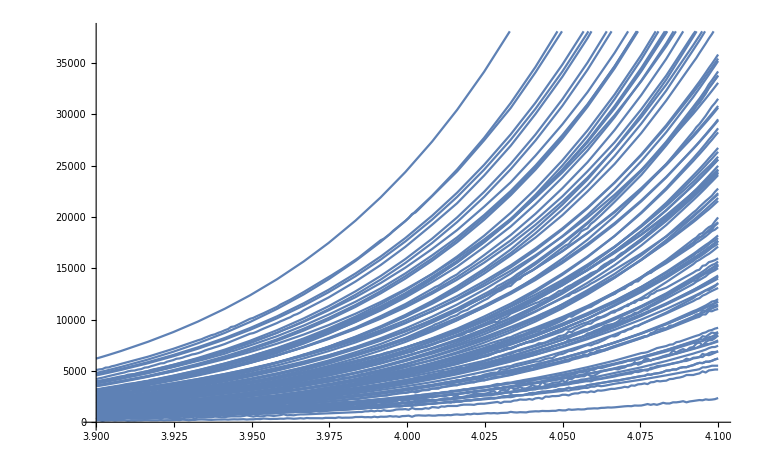

```mathematica
Plot[Table[f,{f,Take[chromials,-100]}],{x,3.9,4.1},PerformanceGoal->"Speed"]
```

```mathematica
baseCoeff=Monitor[Table[CompleteBaseCoeff[f]+1,{f,chromials}],f]
```

{{1,1,1,1,3729,38285108,9781354758,357639696465,3723112101278,15571988968421,31897656061195,36243675442297,24821331309531,10850115772579,3151068179652,624932765295,86128826553,8319992815,563043621,26394619,834767,16907,198,2},1893,{1,1,1,1,69,160350,-92908103/8,-39835120087/24,-84131557840/3,-1269032658553/8,-9730252365815/24,-13175842147771/24,-5218740040891/12,-1722595811409/8,-1673573202715/24,-45709263806/3,-13748330047/6,-958590507/4,-34889845/2,-3499437/4,-707045/24,-2527/4,-163/24,23/24}}
 |  |  |  |

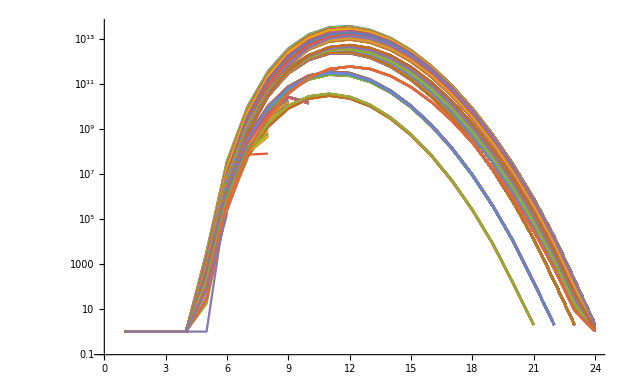

```mathematica
ListLogPlot[baseCoeff, Joined->True, PerformanceGoal->"Quality"]
```